Trees

## Introduction

This chapter is devoted to exploring the computational aspects of the study of trees. Recall from the textbook that a tree is a connected simple graph with no simple circuits.

First, we will discuss how to represent, display, and work with trees using the Wolfram Language. Specifically, we will see how to represent rooted trees and ordered rooted trees in addition to simple trees. We then use these representations to explore many of the topics discussed in the textbook. In particular, we will see how to use binary trees to store data in such a way as to make searching more efficient and we will see an implementation of Huffman codes. We will use Mathematica to carry out the different tree traversal methods described in the text. We will see how to construct spanning trees using both depth-first and breadth-first search and how to use backtracking to solve a variety of interesting problems. Finally, we will implement Prim’s algorithm and Kruskal’s algorithm for finding spanning trees of minimum weight for a weighted graph.

## 11.1 Introduction to Trees

In this section, we will focus on how to construct trees in Mathematica and how to check basic properties, such as determining if a tree is balanced or not. To begin, we will consider the simplest case, unrooted trees, before moving on to rooted and ordered trees.

### Unrooted Trees

Recall that a tree is defined to be a graph that is undirected, connected, and has no simple circuits (or cycles). To create a tree, we can just create a Graph as we did in the previous chapter.

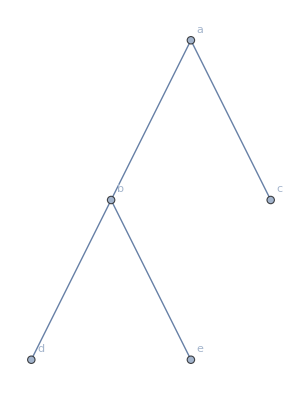

```mathematica
firstTree=Graph[{"a"->"b","a"->"c","b"->"d","b"->"e"},DirectedEdges->False,VertexLabels->"Name"]
```

The first thing you may notice is that Mathematica has automatically drawn this in the traditional way, which suggests that Mathematica recognized the graph as a tree. The TreeGraphQ function can be used to check if a graph is a tree.

```mathematica
TreeGraphQ[firstTree]
```

True

Note that the order of the vertices can affect which vertex appears at the top of the tree. For example, in the tree above, we can ensure that the vertex b is drawn at the top of the tree by giving a list of the vertices as the first argument. We list the vertices in layered order, that is, the top vertex will be first, followed by the vertices we wish to see in the second layer, then the vertices in the third layer and so forth. Note that changing the order of vertices within a layer can affect their horizontal position.

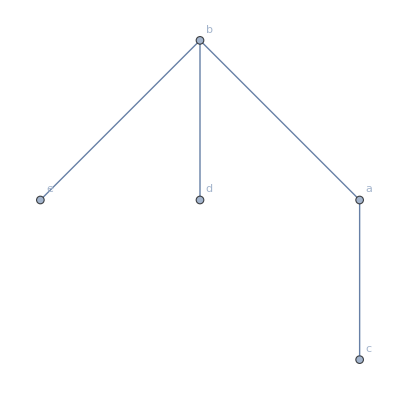

```mathematica
secondTree=Graph[{"b","e","d","a","c"},{"a"->"b","a"->"c","b"->"d","b"->"e"},DirectedEdges->False,VertexLabels->"Name"]
```

However, there is a limit to the amount of influence this provides. For example, Mathematica has a strong preference for shorter, more balanced, trees. Attempting to use the vertex order to create a deeper tree will often be ignored. For example, below we attempt, and fail, to get e at the top of the tree.

```mathematica
Graph[{"e","b","d","a","c"},{"a"->"b","a"->"c","b"->"d","b"->"e"},DirectedEdges->False,VertexLabels->"Name"]
```

-Graphics-

The Wolfram Language provides functions for creating certain kinds of trees. Recall that a rooted tree is called k-ary if every vertex has no more than k children. When k=2, we say that it is a binary tree. Also recall that the height of a rooted tree is the maximum number of levels in the tree, that is, the height is the length of the largest path from the root to any other vertex. (The Wolfram Language refers to the tree as having h levels, which is synonymous with height h.) Given the height as the first argument and k as the second, the function CompleteKaryTree produces the complete k-ary tree of height h. If the second argument is omitted, it defaults as 2, producing a complete binary tree of the specified height.

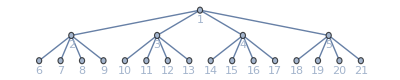

```mathematica
CompleteKaryTree[3,4,VertexLabels->Placed["Name",Below]]
```

### Rooted Trees

Next, we consider rooted trees. Recall that a rooted tree is a directed graph whose underlying undirected graph is a tree and in which one vertex is designated as the root and all edges are directed away from the root. For example, the graph shown below is a rooted tree.

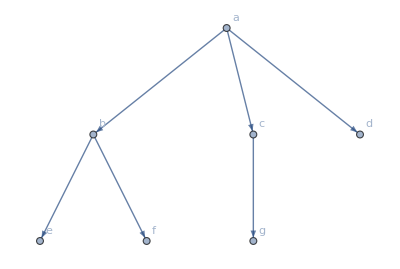

```mathematica
firstRooted=Graph[{"a"->"b","a"->"c","a"->"d","b"->"e","b"->"f","c"->"g"},VertexLabels->"Name"]
```

Note that Mathematica drew this graph as a tree, just as you would hope. Once again, TreeGraphQ will identify this as a tree.

```mathematica
TreeGraphQ[firstRooted]
```

True

While Mathematica does recognize trees with directed edges, it does not automatically respect a root. When drawing the tree, the emphasis is on minimizing the height, as the following example illustrates:

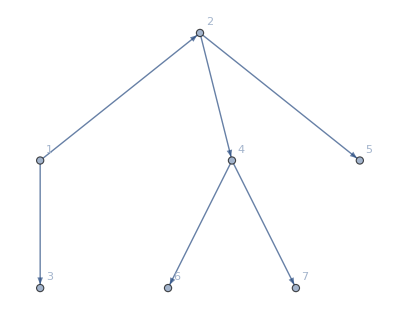

```mathematica
secondRooted=Graph[{1->2,1->3,2->4,2->5,4->6,4->7},VertexLabels->"Name"]
```

Mathematica has drawn this tree with 2 at the top of the image, despite the fact that it does not satisfy the definition of a root, as it has an edge directed towards it.

To draw the tree as intended, we can use the GraphLayout option. There are a wide variety of possibly layouts that can be specified with this option; the values most relevant for trees are “LayeredDigraphEmbedding” and “LayeredEmbedding” with the former appropriate for trees with directed edges. When “LayeredEmbedding” is used as the layout, a vertex will be chosen automatically based on layout considerations, for example, to minimize the tree’s height. When “LayeredDigraphEmbedding” is chosen for a tree with directed edges, the root is the vertex with in–degree 0.

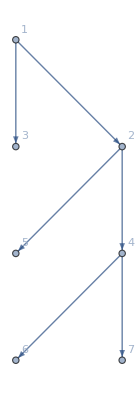

```mathematica
Graph[secondRooted,GraphLayout->"LayeredDigraphEmbedding"]
```

Whether the edges are directed or not, you can specifically designate the root. This is done by giving the GraphLayout option the value {“LayeredEmbedding”, “RootVertex” → root}, where root is the name of the vertex you wish to have considered the root. “LayeredDigraphEmbedding” can also be used, but then both the designated vertex and the natural root will be positioned at the top of the image.

Compare the original drawings of secondRooted and secondTree with the results of choosing roots.

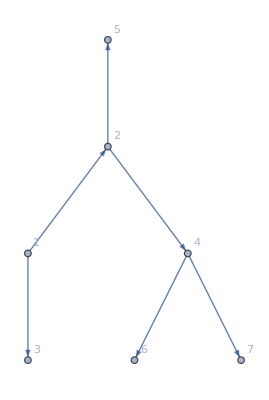

```mathematica
Graph[secondRooted,GraphLayout->{"LayeredEmbedding","RootVertex"->5}]
```

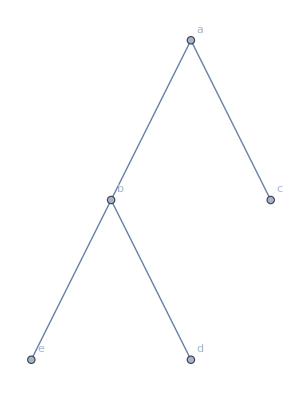

```mathematica
Graph[secondTree,GraphLayout->{"LayeredEmbedding","RootVertex"->"a"}]
```

Another option for controlling the drawing of trees is TreePlot. This is related to the GraphPlot function discussed in the previous chapter. These functions are largely outdated, but are worth being aware of. TreePlot accepts up to three arguments, in addition to options. The first argument is a list of edges that form the tree. The first argument can also be a Graph object. The second argument, which is optional, specifies where the root of the tree should be drawn. Possible positions are: Top, Bottom, Left, Right, and Center. The third argument, which is also optional, can only be used when the second is present and specifies one of the vertices in the tree to be the root. After all arguments are given, you may additional options, such as VertexLabeling. The following example illustrates how to draw secondRooted with the root 1 in its proper position with TreePlot:

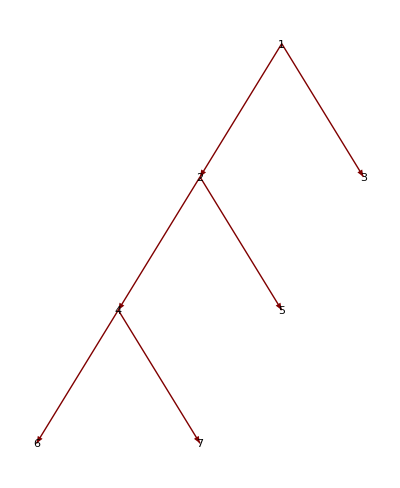

```mathematica
TreePlot[secondRooted,Top,1,VertexLabeling->True]
```

#### Identifying Roots and Rooted Trees

As mentioned earlier, the Wolfram Language’s TreeGraphQ will tell you if a graph is a tree. For directed graphs, it will return false if the graph is not a rooted tree. However, the Wolfram Language does not include a function for finding the root of a rooted tree.

We begin by creating an example of a directed graph which is not a rooted tree, but whose underlying undirected graph is a tree.

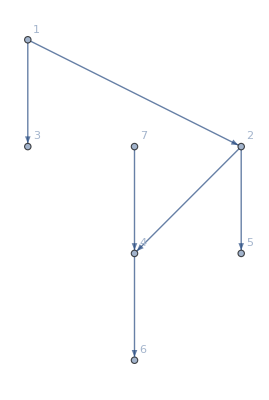

```mathematica
notRooted=Graph[{1->2,1->3,2->4,2->5,4->6,7->4},VertexLabels->"Name"]
```

This is identical to secondRooted, except for the direction of the edge between vertex 4 and vertex 7. Note that TreeGraphQ correctly identifies it as not being a tree, since there are two vertices which are not the tail of any edge.

```mathematica
TreeGraphQ[notRooted]
```

False

However, the underlying undirected graph is a tree.

```mathematica
TreeGraphQ[UndirectedGraph[notRooted]]
```

True

It will be useful to be able to distinguish between a rooted tree and a non-rooted tree. That is, we will need a function that returns True for firstRooted, but False on its undirected underlying graph.

```mathematica
rootedTreeQ[T_Graph]:=TreeGraphQ[T]&&DirectedGraphQ[T]
```

As promised, this distinguishes between firstRooted and its underlying graph.

```mathematica
rootedTreeQ[firstRooted]
```

True

```mathematica
rootedTreeQ[UndirectedGraph[firstRooted]]
```

False

The root of a rooted tree is necessarily the unique vertex with in-degree 0. We can use VertexInDegree to obtain a list of the in-degrees of the vertices of a directed graph.

```mathematica
VertexInDegree[firstRooted]
```

{0,1,1,1,1,1,1}

The Position function, applied to the list of in-degrees, will tell us at which location the 0 appears. Note that the output of Position is a list of the position specifications, themselves lists.

```mathematica
Position[VertexInDegree[firstRooted],0]
```

{{1}}

Since TreeGraphQ has identified this as a tree, we know that there will be exactly one vertex with in-degree 0, so we confidently use Part ([[…]]) to obtain the root’s position in the list.

```mathematica
Position[VertexInDegree[firstRooted],0][[1,1]]
```

1

Since the output of VertexInDegree matches the order of vertices from VertexList, we can use the previous result with Part ([[…]]) and VertexList to obtain the name of the root.

```mathematica
VertexList[firstRooted][[
Position[VertexInDegree[firstRooted],0][[1,1]]
]]
```

a

We create a function based on this example.

```mathematica
findRoot[G_?rootedTreeQ]:=VertexList[G][[Position[VertexInDegree[G],0][[1,1]]]]
```

With this function in hand, we can easily automate the use of TreePlot to draw a rooted tree in its proper form.

```mathematica
rootedTreePlot[G_?rootedTreeQ,opts___]:=TreePlot[G,Top,findRoot[G],opts]
```

We use this function to draw secondRooted.

```mathematica
rootedTreePlot[secondRooted,VertexLabeling->True]
```

-Graphics-

### Specifying Trees with TreeGraph

The Wolfram Language includes a function specifically designed for creating a tree: TreeGraph. This function can be given the same arguments you normally provide Graph, but provides another option for specifying a tree. Specifically, TreeGraph will create a tree based on a list of the tree’s vertices followed by a list of the same length consisting of the parent of each vertex, with the root being listed as its own parent. As an example, we recreate secondTree.

```mathematica
secondTree
```

-Graphics-

```mathematica
TreeGraph[{"b","e","d","a","c"},{"b","b","b","b","a"},VertexLabels->"Name"]
```

-Graphics-

### Parents, Children, Leaves, and Internal Vertices of Rooted Trees

We now consider functions related to identifying particular vertices in a rooted tree. We will be using firstRooted as an example, so we include the image here for reference.

```mathematica
firstRooted
```

-Graphics-

We begin with the question of whether one vertex is the parent of another. Given the two vertices, checking this requires determining whether the directed edge from the parent to the child is actually in the tree.

```mathematica
parentQ[T_?rootedTreeQ,p_,c_]:=EdgeQ[T,DirectedEdge[p,c]]
```

```mathematica
parentQ[firstRooted,"b","f"]
```

True

```mathematica
parentQ[firstRooted,"b","d"]
```

False

Next, we consider the question of finding the parent of a given vertex. This can be done by searching the output of EdgeList for the edge that have the given vertex at the terminal end. Assuming the graph is in fact a rooted tree, there can be at most one such edge. If the vertex is the root, there will be no parent and the function will return Null. Note the second argument in Cases means that it will search the edge list for those edges from the variable p to the given edge v but will put only p in the output.

```mathematica
findParent[T_?rootedTreeQ,v_]:=Module[{P,p},
P=Cases[EdgeList[T],DirectedEdge[p_,v]->p];
If[Length[P]≠1,Null,P[[1]]]
]
```

```mathematica
findParent[firstRooted,"d"]
```

a

```mathematica
findParent[firstRooted,"a"]
```

For the related question of determining all children of the given vertex, we take the same approach but with the given vertex at the initial end.

```mathematica
findChildren[T_?rootedTreeQ,v_]:=Module[{c},Cases[EdgeList[T],DirectedEdge[v,c_]->c]]
```

```mathematica
findChildren[firstRooted,"a"]
```

{b,c,d}

```mathematica
findChildren[firstRooted,"f"]
```

{}

The findChildren function also indicates how we can test a vertex to determine if it is an internal vertex or a leaf.

```mathematica
internalVertexQ[T_?rootedTreeQ,v_]:=Length[findChildren[T,v]]≠0
```

```mathematica
leafQ[T_?rootedTreeQ,v_]:=Length[findChildren[T,v]]==0
```

```mathematica
internalVertexQ[firstRooted,"a"]
```

True

```mathematica
leafQ[firstRooted,"a"]
```

False

```mathematica
leafQ[firstRooted,"f"]
```

True

We can determine all the leaves of a given tree by testing each vertex with leafQ. Here we use Select in order to test all of the vertices of the graph with a pure Function (&) based on leafQ.

```mathematica
findLeaves[T_?rootedTreeQ]:=Module[{V},
V=VertexList[T];
Select[V,leafQ[T,#]&]
]
```

```mathematica
findLeaves[firstRooted]
```

{d,e,f,g}

### Ordered Rooted Trees

Recall that an ordered rooted tree is a rooted tree in which the children of each internal vertex are ordered.

#### Representing Ordered Rooted Trees

To represent an ordered rooted tree in the Wolfram Language, we will need to store the order of children. There are many ways to accomplish this, but perhaps the most straightforward is to mark each vertex with its order among its siblings. By way of illustration, we make an ordered version of firstRooted.

```mathematica
firstRooted
```

-Graphics-

Mathematica draws the vertices in left-to-right order based on the order in which they appear in the list of vertices. Suppose we wanted the children of a to be in the order c, b, d, and the children of b to be in the order f then e. We will represent child order by assigning, for each vertex, a property called "order." We set the order of the root to be 0, and for all other vertices, the order attribute will represent the position of that vertex among its siblings. In our example, c will have "order" 1, b will have "order" 2, and d will have "order" 3. We define a function that uses PropertyValue to set the "order" property for each vertex.

The first argument to this function will be the name of a rooted tree. The second argument will be an Association whose keys are the vertices of the tree and whose values are the orders. The function will loop through the vertices of the tree and set the “order” property.

```mathematica
setChildOrder::argx="Association keys do not match vertices.";
setChildOrder[G_?rootedTreeQ,order_Association]:=Module[{T=G,v},
Check[
If[Union[Keys[order]]≠Union[VertexList[G]],Message[setChildOrder::argx]],Return[$Failed]];
Do[PropertyValue[{T,v},"order"]=order[v],{v,VertexList[T]}];
T
]
```

Note that this function outputs a new graph, it does not modify the original input, so we will need to make an assignment to the output.

```mathematica
orderedAttempt=setChildOrder[firstRooted,<|"a"->0,"b"->2,"c"->1,"d"->3,"e"->2,"f"->1,"g"->1|>]
```

-Graphics-

Note that the vertices in orderedAttempt now have the “order” property set, but we still need to make the tree be drawn in the appropriate way.

#### A Test for Ordered Rooted Trees

Now that we know how to represent an ordered rooted tree in the Wolfram Language, we will create a function to test a graph object and ensure that it does in fact represent an ordered rooted tree. This will help us make the functions we write later be more robust. The requirement for being an ordered rooted tree are: the object must be a tree, it must be directed, every vertex must have the order property set, and the root’s order must be 0.

```mathematica
orderedRootedTreeQ[T_]:=Module[{v},
Catch[
If[!rootedTreeQ,Throw[False]];
Do[If[PropertyValue[{T,v},"order"]===$Failed,Throw[False]]
,{v,VertexList[T]}];
If[PropertyValue[{T,findRoot[T]},"order"]≠0,Throw[False]];
Throw[True]
]
]
```

```mathematica
orderedRootedTreeQ[firstRooted]
```

False

```mathematica
orderedRootedTreeQ[orderedAttempt]
```

True

#### Drawing Ordered Rooted Trees

While orderedAttempt is now officially an ordered rooted tree and is storing the order of children, it will not be drawn with children in the proper order. To influence the order in which the vertices appear in the drawing, we will use the fact that Mathematica draws vertices in the same order as is output by VertexList. Consider the following example:

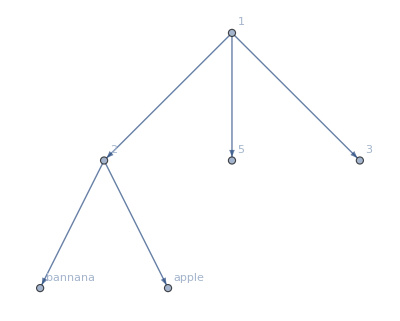

```mathematica
orderExample1=Graph[{1->2,1->5,1->3,2->"bannana",2->"apple"},VertexLabels->"Name"]
```

```mathematica
VertexList[orderExample1]
```

{1,2,5,3,bannana,apple}

The order of the vertex list is determined by the order of the edges. For example, the edge 1→5 appears before the edge 1→3 in the definition of the Graph, so vertex 5 appears before vertex 3. When drawing the tree, Mathematica uses the order of the vertices in the vertex list to determine the relative positions of vertices within a level. In the above, since vertex 5 appears before vertex 3, it also appears to the left.

By explicitly providing a list of vertices as an argument to Graph, we can influence the positions in the image.

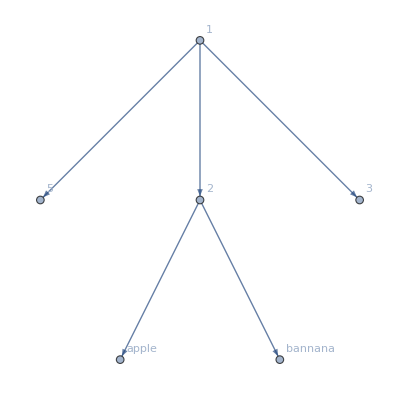

```mathematica
orderExample2=Graph[{1,5,2,3,"apple","bannana"},{1->2,1->5,1->3,2->"bannana",2->"apple"},VertexLabels->"Name"]
```

We will use this feature in order to properly draw ordered rooted graphs. Given the data for an ordered rooted tree, we will sort the vertices based on the order property.

Our function will accept as arguments a list of vertices (in any order), a list of edges (given as rules or directed edges), an association specifying the order property for each vertex, and graph options. The first task is to ensure that the input is valid, which we do by applying Graph to the vertices and edges and applying rootedTreeQ, and then ensuring that the keys of the association agree with the collection of vertices.

Once we know that the input is reasonably valid, we extract the root using the findRoot function we created earlier. This is needed so that we can specify the root in conjunction with the “LayeredEmbedding” layout.

To order the vertices, we use Sort with a Function (&) as the second argument that compares the values from the association. This means that the root will be the first element in this list, all the first children will appear after the root, then all the second children, etc.

Once the vertex list is properly ordered, we then wrap the name of each vertex within Property. When creating a Graph, you can wrap a vertex or edge in Property with second argument a rule (or list of rules) assigning values to properties. Here, this saves us from having to build the graph and then assign the “order” property with a loop. Instead, Property allows us to assign the order at the time of the graph creation. The resulting list of vertices is passed to Graph along with the edges and any options.

```mathematica
orderedTree::argx="Vertices and edges do not form a rooted tree.";
orderedTree[V_List,edges:{___Rule|___DirectedEdge},order_Association,opts___]:=Module[{sortedV,root},
Check[If[!rootedTreeQ[Graph[V,edges]],Message[orderedTree::argx]],Return[$Failed]];
Check[If[Union[Keys[order]]≠Union[V],Message[setChildOrder::argx]],Return[$Failed]];
sortedV=Sort[V,order[#1]<order[#2]&];
root=sortedV[[1]];
sortedV=Map[Property[#,"order"->order[#]]&,sortedV];
Graph[sortedV,edges,GraphLayout->{"LayeredEmbedding","RootVertex"->root},opts]
]
```

With this function in place, it is a simple matter to create a version that does not require the list of vertices, and another that will take a Graph as input. These take advantage of the Wolfram Language’s flexibility in allowing symbols to be overloaded with different signatures.

```mathematica
orderedTree[edges:{___Rule|___DirectedEdge},order_Association,opts___]:=
orderedTree[Union[Flatten[List@@@edges]],edges,order,opts]
```

```mathematica
orderedTree[g_Graph,order_Association,opts___]:=orderedTree[VertexList[g],EdgeList[g],order,opts]
```

Finally, we can draw our ordered tree correctly. Note that to retain the order, we make an explicit reassignment of the symbol.

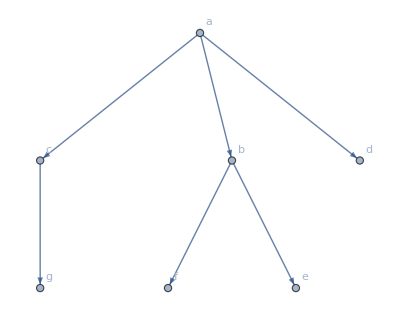

```mathematica
firstOrdered=orderedTree[firstRooted,<|"a"->0,"b"->2,"c"->1,"d"->3,"e"->2,"f"->1,"g"->1|>,VertexLabels->"Name"]
```

It is also useful to have a function which, like VertexList and EdgeList , will obtain the association representing the vertex order from a Graph representing an ordered tree. This simply requires extracting the order property from each vertex and producing the association.

```mathematica
orderAssociation[T_?orderedRootedTreeQ] :=Module[{v},
Association@@Table[v->PropertyValue[{T,v},"order"],{v,VertexList[T]}]
]
```

### Properties of Trees

We conclude this section with functions for calculating the level of a vertex, the height of a tree, and for determining if a tree is balanced or not.

The level of a vertex in a rooted tree is the length of the path from the root to the vertex. We compute the level in reverse. We first initialize a counter to 0. If the given vertex is the root, then the level is 0. Otherwise, increment the counter and look at the parent of the original vertex. If this vertex is the root, then the counter holds the level. Otherwise, increment the counter and back up to the parent of the current vertex. When we reach the root, then the value of the counter is the level of the vertex.

```mathematica
findLevel[T_?rootedTreeQ,V_]:=Module[{v,level},
level=0;
v=V;
While[findParent[T,v]=!=Null,
level++;
v=findParent[T,v]
];
level
]
```

We can compute the levels of g and d in the firstOrdered tree.

```mathematica
findLevel[firstOrdered,"g"]
```

2

```mathematica
findLevel[firstOrdered,"d"]
```

1

The height of a tree is the maximum of the levels of the vertices. We can compute the height by checking each vertex’s level. We use a variable to hold the largest level and each time we find a vertex with a level larger than the current maximum, we update the variable.

```mathematica
findHeight[T_?rootedTreeQ]:=Module[{v,height,level},
height=0;
Do[level=findLevel[T,v];
If[level>height,height=level]
,{v,VertexList[T]}];
height
]
```

```mathematica
findHeight[firstOrdered]
```

2

Recall that a rooted tree of height h is balanced if all leaves are at level h or h-1. To determine if a given tree is balanced, we need to: (1) calculate the height of the tree, (2) find all the leaves of the tree with the findLeaves function we wrote earlier, and (3) test each leaf’s level and return False if it is higher than level h-1.

```mathematica
balancedTreeQ[T_?rootedTreeQ]:=Module[{height,leaves,v},
height=findHeight[T];
leaves=findLeaves[T];
Catch[
Do[If[findLevel[T,v]<height-1,Throw[False]]
,{v,leaves}];
Throw[True]
]
]
```

We see that our firstOrdered tree is balanced.

```mathematica
balancedTreeQ[firstOrdered]
```

True

## 11.2 Applications of Trees

This section is concerned with applications of trees, particularly binary trees. Specifically, we consider the use of trees in binary search algorithms as well as in Huffman codes. The reason we use binary trees is that we can use the binary structure of the tree to make binary decisions (e.g., less than/greater than) regarding search paths or insertion of elements. Additionally, the binary tree structure corresponds well with the way computers store information as binary data.

Recall that a tree is called a binary tree if all vertices in the tree have at most two children. In this section, we will be using ordered binary trees. The fact that the vertices are ordered means that the children of a vertex can be considered to be either a left child or a right child. By convention, we consider the left child to be the first child and the right child to be second.

### Representation in the Wolfram Language

Before we get to the applications, we will discuss how we can represent binary trees in the Wolfram Language and develop some functions to help us manipulate them. Since a binary tree is a particular kind of ordered rooted tree, our work here should be consistent with what we did above.

#### A Binary Tree Predicate

We will construct a predicate, binaryTreeQ to test whether a graph represents a binary tree. We will impose three conditions for an object to be considered a binary tree. First, it must be an ordered rooted tree, that is, it must pass orderedRootedTreeQ. Second, it must be binary, that is, each vertex must have at most two children. Third, each vertex other than the root must have order attribute 1 or 2, with 1 indicating that the vertex is a left child and 2 for right. The root will have its order attribute set to 0.

First, we construct an example of a binary tree. The tree we construct is the binary search tree for the letters D, B, F, A, C, E.

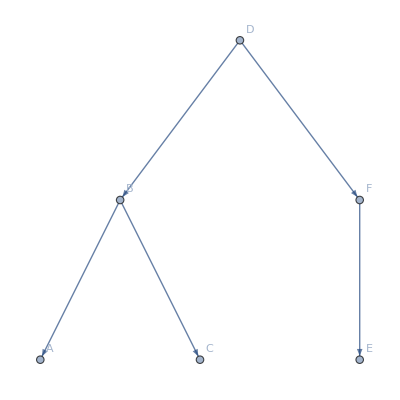

```mathematica
firstBinaryTree=orderedTree[{"D","B","F","A","C","E"},{"D"->"B","D"->"F","B"->"A","B"->"C","F"->"E"},<|"D"->0,"B"->1,"F"->2,"A"->1,"C"->2,"E"->1|>,VertexLabels->"Name"]
```

Now that we have an example, we will create the test. To check that the tree is in fact binary, we can use the VertexOutDegree function to count the number of children of each vertex. If any vertex has more than two children, then the tree is not binary. Moreover, we make sure that each vertex is marked with an order of 1 or 2, or 0 in the case of the vertex.

```mathematica
binaryTreeQ[T_Graph]:=Module[{R,v,vpos},
Catch[
If[!orderedRootedTreeQ[T],Throw[False]];
R=findRoot[T];
Do[
If[VertexOutDegree[T,v]>2,Throw[False]];
vpos=PropertyValue[{T,v},"order"];
If[(vpos==0&&v≠R)||(vpos≠0&&vpos≠1&&vpos≠2),Throw[False]]
,{v,VertexList[T]}];
Throw[True]
]
]
```

The tree we just constructed is binary, but the example of an ordered tree from the previous section had a root with three children and thus is not binary.

```mathematica
binaryTreeQ[firstBinaryTree]
```

True

```mathematica
binaryTreeQ[firstOrdered]
```

False

#### Modifying arguments with HoldFirst

Next, we will write a function for drawing binary trees. In a binary tree, it is important to distinguish between a vertex being a left child versus a right child, even when it has no sibling. Therefore, the image of such a tree should reflect that, rather than placing only children directly below their parent.

The function we create will be called drawBinaryTree. Because the purpose of this function is to modify the locations of where vertices are drawn in a binary tree and because there is a canonical way to display binary trees, it is natural to develop this function in such a way as to change its argument, rather than needing to make an assignment to the result of the function.

We use the HoldFirst attribute to make arguments modifiable. Normally when you provide an argument to a function, the function cannot assign to the argument. Consider the following simple function:

```mathematica
five=5
```

5

```mathematica
addOne[n_]:=n=n+1
```

```mathematica
addOne[five]
```

Set::setraw: Cannot assign to raw object 5.

6

This function produces an error when we attempt to assign a value to the argument n. This is a feature of the Wolfram Language that is designed to encourage good programming practices. In particular, for a function to modify one of its arguments, we need to be very explicit that we really want to do so. This helps prevent unintended consequences—accidentally modifying an argument can cause serious errors in your work.

You can think about what is going on in the addOne function this way: when you call the function with the syntax addOne[five], all of the occurrences of the name n are resolved to the object 5, which is the value stored in five. That is, the command n=n+1 resolves to 5=5+1. Clearly that is not a legal command.

The HoldFirst attribute provides a way around this. If we attach the HoldFirst attribute to addOne, by applying SetAttributes to the function name and the attribute, we are telling Mathematica to not resolve the parameter n into the object it refers to, but to evaluate the argument into a symbol. Instead of evaluating the symbol five to get the object 5 and replacing the parameter n with 5, the symbol five is held, and the parameter n is replaced with the symbol five. This means that the command becomes five=five+1.

```mathematica
SetAttributes[addOne2,HoldFirst];
addOne2[n_]:=n=n+1
```

Now, we can see that this function modifies the variable it is given.

```mathematica
five
```

5

```mathematica
addOne2[five]
```

6

```mathematica
five
```

6

In summary, we can create functions that modify an argument that is passed as a symbol by applying SetAttributes to the function name and the attribute HoldFirst. This allows the parameter to appear on the left side of an assignment and modify the symbol passed as input to the function.

#### Drawing Binary Trees

We are now ready to write a function for drawing binary trees. Note that, while orderedTree will result in an image in which the children are drawn correctly relative to each other, vertices that are the only child will appear directly below their parent rather than to the left or right. Here, we take more control over the locations by explicitly calculating the position of each vertex.

Think about the tree as being drawn in a 1 by 1 box with (0,0) at the bottom left corner. The y-coordinate of each vertex will depend on the height of the tree and the level of the vertex. Specifically, the y-coordinate of any vertex is 1-l/h, where l is the level of the vertex and h is the height of the tree. This way, the root, which is at level 0, has y-coordinate 1 and the vertices in the last level have y-coordinate 0.

For the x-coordinates, the position of the vertex depends on the position of its parent and its level. We start by setting the x-position of the root to 1/2. The left child of the root will be drawn at x-coordinate 1/4 and the right child at 3/4. We can think about the children of the root as being drawn 1/4 to the left of the root and 1/4 to the right of the root, respectively. That is, the x-coordinate of the root’s left child is 1/2-1/4. and the x-coordinate of the right child is 1/2+1/4. Generally, for a vertex in level l, we can calculate its x-coordinate as the x-coordinate of its parent plus (for right children) or minus (for left) 1/2^(l+1).

The drawBinaryTree function is given below. The first thing the function does is to set the VertexCoordinates property for the entire tree by extracting the existing positions of vertices with GraphEmbedding. The Wolfram Language does not allow us to manipulate VertexCoordinates individually when they have been automatically assigned by a layout. We get around this by setting explicit values to whatever positions the layout had determined.

Then, we calculate the height of the tree with the findHeight function from earlier and find the root with findRoot. The function then processes the root of the tree by setting its position to (1/2,1). We also create a list, verts, and populate it with the root's children.

We then begin a While loop. We initialize a counter i to 1. This counter serves as an index into the verts list. At each step in the loop, we do several things. First, we use the findLevel function to determine the level of the vertex. Second, the y-coordinate is calculated by the formula 1+l/h. Third, the x-coordinate is calculated by accessing the x-coordinate of the parent and adding or subtracting 1/2^(l+1). Fourth, we set the VertexCoordinates property for the vertex. Finally, the children of the current vertex are added to the verts list and the counter is incremented.

```mathematica
SetAttributes[drawBinaryTree,HoldFirst];
drawBinaryTree[T_?binaryTreeQ]:=Module[{height,v,i,level,verts,x,y,parent,side},
PropertyValue[T,VertexCoordinates]=GraphEmbedding[T];
height=findHeight[T];
v=findRoot[T];
PropertyValue[{T,v},VertexCoordinates]={1/2,1};
verts=findChildren[T,v];
i=1;
While[i≤Length[verts],
v=verts[[i]];
level=findLevel[T,v];
y=1-level/height;
parent=findParent[T,v];
x=PropertyValue[{T,parent},VertexCoordinates][[1]];
side=Switch[PropertyValue[{T,v},"order"],1,-1,2,1];
x=x+side*1/(2^(level+1));
PropertyValue[{T,v},VertexCoordinates]={x,y};
verts=Join[verts,findChildren[T,v]];
i++
];
T
]
```

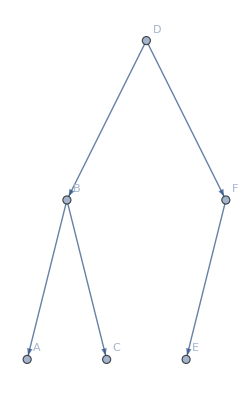

```mathematica
drawBinaryTree[firstBinaryTree]
```

We can also use drawBinaryTree within functions that produce a binary tree from vertex and edge data.

```mathematica
binaryTree::argx="Arguments do not form a binary tree.";
binaryTree[V_List,edges:{___Rule|___DirectedEdge},order_Association,opts___]:=Module[{T},
T=orderedTree[V,edges,order,opts];
Check[If[!binaryTreeQ[T],Message[binaryTree::argx]],Return[$Failed]];
drawBinaryTree[T]
];
binaryTree[edges:{___Rule|___DirectedEdge},order_Association,opts___]:=binaryTree[Union[Flatten[List@@@edges]],edges,order,opts];
binaryTree[g_Graph,order_Association,opts___]:=binaryTree[VertexList[g],EdgeList[g],order,opts];
```

#### Parents and Children

In the previous section, we created the function findParent, which returns the parent of a given vertex in the given tree. This function works on binary trees just as well.

```mathematica
findParent[firstBinaryTree,"C"]
```

B

We had also created the findChildren function, which we can also use with binary trees. However, for binary trees, we will want to be more specific and be able to determine the left and right children of a given vertex. Finding the left (respectively, right) child of a given vertex can be done by looking at each child of the vertex and checking the order attribute. The child with order 1 is the left child and is returned by the function (respectively, 2 and right child). If there is no left (respectively, right), child, the function will return Null.

```mathematica
findLeftChild[T_?binaryTreeQ,v_]/;VertexQ[T,v]:=Module[{children,w,pos},
children=findChildren[T,v];
Catch[
Do[pos=PropertyValue[{T,w},"order"];
If[pos==1,Throw[w]]
,{w,children}];
Throw[Null]
]
]
```

```mathematica
findRightChild[T_?binaryTreeQ,v_]/;VertexQ[T,v]:=Module[{children,w,pos},
children=findChildren[T,v];
Catch[
Do[pos=PropertyValue[{T,w},"order"];
If[pos==2,Throw[w]]
,{w,children}];
Throw[Null]
]
]
```

```mathematica
findLeftChild[firstBinaryTree,"F"]
```

E

```mathematica
findRightChild[firstBinaryTree,"F"]
```

#### Building Binary Trees

We will also want functions to create and build up a binary tree. Specifically, we will create a function that, given the label for the root of a binary tree, creates the tree with that vertex as its root. We will then write functions that, given a binary tree, a vertex in the tree, and a label for a new vertex, adds the new vertex as the left or right child of the given vertex.

The newBinaryTree function creates the binary tree consisting of a single vertex, the root of the tree. This function also accepts a list of options to be passed to the Graph.

```mathematica
newBinaryTree[r_,opts___]:=binaryTree[{r},{},<|r->0|>,opts]
```

Adding a child to a vertex in a binary tree requires three basic steps. We must add a vertex, add a directed edge from the parent to the new vertex, and then identify the new child as left or right by setting the order attribute to 1 or 2, respectively. We precede building the new tree by ensuring that there is not already a child vertex in the position already.

```mathematica
addLeftChild[T_?binaryTreeQ,v_,newV_]/;VertexQ[T,v]:=Module[{vertexL,edgeL,orderA},
If[findLeftChild[T,v]≠Null,Return[$Failed]];
vertexL=Append[VertexList[T],newV];
edgeL=Append[EdgeList[T],DirectedEdge[v,newV]];
orderA=Append[orderAssociation[T],newV->1];
binaryTree[vertexL,edgeL,orderA]
]
```

```mathematica
addRightChild[T_?binaryTreeQ,v_,newV_]/;VertexQ[T,v]:=Module[{vertexL,edgeL,orderA},
If[findRightChild[T,v]≠Null,Return[$Failed]];
vertexL=Append[VertexList[T],newV];
edgeL=Append[EdgeList[T],DirectedEdge[v,newV]];
orderA=Append[orderAssociation[T],newV->2];
binaryTree[vertexL,edgeL,orderA]
]
```

With newBinaryTree, addLeftChild, and addRightChild, we can now construct binary trees one vertex at a time. We will illustrate this by creating the binary search tree described in Example 1 of the text by following the steps illustrated in Figure 1. We abbreviate the words in order to make the image more readable.

```mathematica
fig1Tree=newBinaryTree["Math"];
fig1Tree=addRightChild[fig1Tree,"Math","Phys"];
fig1Tree=addLeftChild[fig1Tree,"Math","Geog"];
fig1Tree=addRightChild[fig1Tree,"Phys","Zoo"];
fig1Tree=addLeftChild[fig1Tree,"Phys","Meteo"];
fig1Tree=addRightChild[fig1Tree,"Geog","Geol"];
fig1Tree=addLeftChild[fig1Tree,"Zoo","Psy"];
fig1Tree=addLeftChild[fig1Tree,"Geog","Chem"];
```

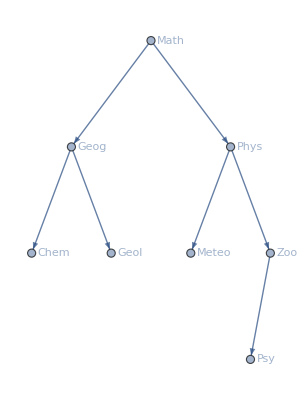

```mathematica
Graph[fig1Tree,VertexLabels->Placed["Name",After]]
```

### Binary Insertion

A key benefit of binary search trees is that the search time required to find a specific element of the tree is logarithmic in the number of vertices of the tree. The drawback is that the initial insertion of a vertex is more expensive.

The procedure for constructing a binary search tree by insertion is described in Algorithm 1 in Section 11.2 of the textbook. We will implement this algorithm as the function binaryInsertion.

The binaryInsertion function will accept two input values: a binary search tree and a vertex to be found or added. The function returns True if the vertex is found to already be in the tree, and if not, it will add the vertex to the tree and return False.

We begin by locating the root of the tree and setting the local variable v to the root. Then, we begin a While loop. This loop continues provided two conditions are met. First, that v is not Null. If we discover that the value we are searching for is not in the tree, then we will add it to the tree and set v to Null, to indicate that we had to add a vertex, and this terminates the While loop. The second condition is that v is not x, where x is the value we are searching for. If v=x, then we have found the vertex and thus the loop should terminate. (Note that the Wolfram Language identifies a vertex with its name, so, unlike the text, we do not distinguish between v and its label.)

Within the While loop, there are two possibilities. Either the sought-after value is less than v or it is greater than v. They cannot be equal because that is one of the terminating conditions for the While loop. If the target value is less than v, then we consider the left child of v. If there is no left child, then we know that the value is not in the tree and so we add the value as the left child of v and then set v to Null to indicate that the desired value was not already in the tree. If there is a left child, then we set v equal to it and continue the loop. If the target value is greater than v, we proceed in exactly the same way, substituting right for left.

Once the loop terminates, we check the value of v. If v is Null, then we know that the desired value was not found and the algorithm returns False. If v is not Null, then we return True.

Here, now, is the binary insertion algorithm.

```mathematica
SetAttributes[binaryInsertion,HoldFirst];
binaryInsertion[BST_?binaryTreeQ,x_]:=Module[{v},
v=findRoot[BST];
While[v=!=Null&&v≠x,
If[Order[x,v]==1,
If[findLeftChild[BST,v]===Null,
(* no left child *)
BST=addLeftChild[BST,v,x];
v=Null,
(* left child exists *)
v=findLeftChild[BST,v]]
, (* else x>v *)
If[findRightChild[BST,v]===Null,
(* no right child *)
BST=addRightChild[BST,v,x];
v=Null,
(* right child exists *)
v=findRightChild[BST,v]]
]
]; (* end while loop *)
v=!=Null
]
```

Note that we use the Order function to compare x and v. Order returns 1 if the first argument is before (“less than”) the second in the canonical order, that is, alphabetically for strings, numerically for numbers. Order returns -1 if the first argument is after the second, and 0 if they are equal. The Wolfram Language does not allow you to use the less-than operator, Less (<), with strings. Order is generic and will allow string, integer, symbol and even other kinds of vertex names.

Also note that binaryInsertion requires that its argument already be a binary tree. A new tree must be created with newBinaryTree.

Now, we can check if oceanography is in the fig1Tree of academic subjects.

```mathematica
binaryInsertion[fig1Tree,"Oc"]
```

False

The function returned False indicating that “Oc” was not found in the tree. Displaying fig1Tree, we see that it was added as a child of meteorology.

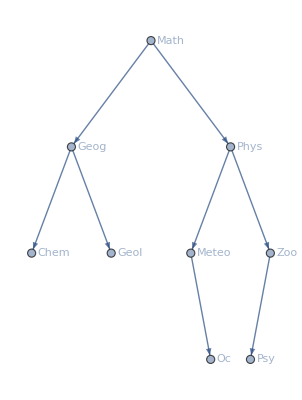

```mathematica
Graph[fig1Tree,VertexLabels->Placed["Name",After]]
```

On the other hand, zoology is already in the tree and so the tree is not modified.

```mathematica
binaryInsertion[fig1Tree,"Zoo"]
```

True

```mathematica
Graph[fig1Tree,VertexLabels->Placed["Name",After]]
```

-Graphics-

#### Constructing a Binary Search Tree from a List

To conclude our discussion of binary search trees, we will create a function that takes a list of values and successively uses the binaryInsertion function to create a binary search tree for the given list.

```mathematica
makeBST[L_List,opts___]:=Module[{T,v},
T=newBinaryTree[L[[1]]];
Do[binaryInsertion[T,L[[i]]],{i,2,Length[L]}];
T=Graph[T,opts]
]
```

We use this to complete Exercise 1 from Section 11.2.

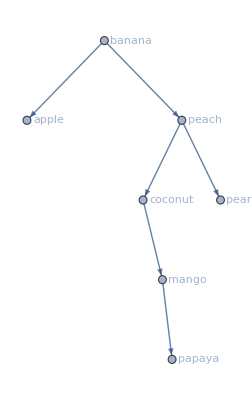

```mathematica
exercise1=makeBST[{"banana","peach","apple","pear","coconut","mango","papaya"},VertexLabels->Placed["Name",After]]
```

### Huffman Coding

Huffman coding is a method for constructing an efficient prefix code for a set of characters. It is based on a greedy algorithm—at each step the vertices with the least weight are combined. It can be shown that Huffman coding produces optimal prefix codes. The algorithm that we will implement is described in Algorithm 2 of Section 11.2.

#### Creating the Initial Forest

We begin with a list of characters (or other kinds of symbol) and their weights, or frequencies. The first step is to create the initial forest, which we implement as a list of trees. For each character, we create the binary tree consisting of a single vertex corresponding to the character.

We create a function, similar to newBinaryTree, which, in addition to creating the binary tree, also assigns a “weight” attribute to the graph to store the weight of the character.

```mathematica
newHTree[s_,w_,opts___]:=Module[{T},
T=newBinaryTree[s];
PropertyValue[T,"weight"]=w;
Graph[T,opts]
]
```

We now write a function to create the initial forest. We assume that the data is provided as a list of pairs consisting of the character and the weight.

```mathematica
createForest[L_List,opts___]:=Module[{forest={},M,v,w,G},
Do[{v,w}=M;
AppendTo[forest,newHTree[v,w,opts]]
,{M,L}];
forest
]
```

Using this function, we form the initial forest for Exercise 23 from Section 11.2. We use the ImageSize option to limit the width of the images. Ordinarily, you would simply suppress the output from this function.

```mathematica
ex23Forest=createForest[{{"a",0.20},{"b",0.10},{"c",0.15},{"d",0.25},{"e",0.30}},VertexLabels->Placed["Name",Above],ImageSize->50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The main work of the Huffman coding algorithm is to determine the two members of the forest with the smallest weights. These two trees are then assembled into a single tree whose root is a new vertex and with the trees with the lowest weight and second lowest weight as the right and left subtrees of the root. The new tree’s weight is the sum of the weights of the two original trees.

#### Sorting the Forest

Recall that the Sort function accepts an optional second argument, specifically, a function on two arguments that returns True if the first argument precedes the second in the desired order. The following function will be of this kind, accepting two binary trees as input and comparing their weights:

```mathematica
compareTrees[A_?binaryTreeQ,B_?binaryTreeQ]:=Module[{a,b},
a=PropertyValue[A,"weight"];
b=PropertyValue[B,"weight"];
a<b
]
```

```mathematica
ex23Forest=Sort[ex23Forest,compareTrees]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Combining Two Trees

Next, we need to take two binary trees and create a new binary tree with one tree as the left subtree of the new root and the other as the right subtree. This function will require three arguments: the name of the new root, the left subtree, and the right subtree.

We create the new tree by: (1) combining the vertex lists of the original trees and adding the new vertex; (2) merging the two sets of edges of the original tress and adding two new edges linking the new root to the previous roots; (3) combining the associations representing the child orders from the original trees and then changing the values for the two original roots to reflect their new status as left and right children in the new tree; (4) creating the new tree; (5) copying the edge labels and assigning the new edges the labels 0 and 1; and (6) setting the “weight” attribute of the new tree to be the sum of the weights of the two original trees.

```mathematica
joinHTrees[newR_,A_?binaryTreeQ,B_?binaryTreeQ,opts___]:=Module[{newT,newVerts,Aroot,Broot,newEdges,newOrders,v,e,p,w},
newVerts=Join[{newR},VertexList[A],VertexList[B]];
Aroot=findRoot[A];
Broot=findRoot[B];
newEdges=Join[EdgeList[A],EdgeList[B],{DirectedEdge[newR,Aroot],DirectedEdge[newR,Broot]}];
newOrders=Join[orderAssociation[A],orderAssociation[B],<|newR->0,Aroot->1,Broot->2|>];
newT=binaryTree[newVerts,newEdges,newOrders,opts];
Do[PropertyValue[{newT,e},EdgeLabels]=PropertyValue[{A,e},EdgeLabels]
,{e,EdgeList[A]}];
Do[PropertyValue[{newT,e},EdgeLabels]=PropertyValue[{B,e},EdgeLabels]
,{e,EdgeList[B]}];
PropertyValue[{newT,DirectedEdge[newR,Aroot]},EdgeLabels]=Placed[0,{.5,{1,0}}];
PropertyValue[{newT,DirectedEdge[newR,Broot]},EdgeLabels]=Placed[1,{.5,{-1,0}}];
w=PropertyValue[A,"weight"]+PropertyValue[B,"weight"];
PropertyValue[newT,"weight"]=w;
newT
]
```

For example, we join the first two graphs in our sorted ex23Forest.

```mathematica
exampleJoin=joinHTrees["newR",ex23Forest[[1]],ex23Forest[[2]],VertexLabels->"Name",ImageSize->100]
```

-Graphics-

#### Implementing the Main Function

We now have the major pieces of the Huffman algorithm assembled and we can write the huffmanCode function. This function will accept as input the same list of character-weight pairs as the createForest function did. The function’s first step is to create the forest F. Then, we begin a While loop that continues as long as the list F contains more than one element. Inside the loop, we first use the compareTrees function to sort the forest in increasing order of weight. Then, we use the joinHTrees function to join the first two trees in the forest and we add that new tree to the list, replacing the original two.

```mathematica
huffmanCode[L_List,opts___]:=Module[{F,i,tempT},
F=createForest[L,opts];
i=0;
While[Length[F]>1,
F=Sort[F,compareTrees];
i++;
tempT=joinHTrees["I"<>ToString[i],F[[2]],F[[1]],opts];
F=Append[F[[3;;-1]],tempT]
];
F[[1]]
]
```

Note that we need a name for the new root when we join two trees. Since these will be the internal vertices of the final tree, we call them I1, I2, I3, etc. We keep a counter i and use the string concatenation operator StringJoin (<>) to create the names of the internal vertices.

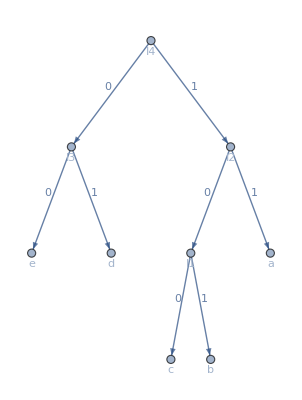

```mathematica
ex23HCode=huffmanCode[{{"a",0.20},{"b",0.10},{"c",0.15},{"d",0.25},{"e",0.30}},VertexLabels->Placed["Name",Below]]
```

#### Encoding Strings Using the Huffman Code Tree

We conclude this section by writing a function to encode a string of characters using a given Huffman tree. Note that you can use Characters to decompose a string into a list of the individual letters. For example,

```mathematica
Characters["Hello"]
```

{H,e,l,l,o}

Since we encode a string by assembling the codes for individual characters, we start with a function for encoding a single character. We assemble the character’s code right to left. Beginning with the vertex corresponding to the desired character, we find that vertex’s order value. The last digit of the code is one less than the order, so that a left child corresponds to order value 1 and code digit 0 while a right child has order value 2 and code digit 1. The next rightmost digit is determined by the order value of the parent vertex. We continue until we reach the root. We use the StringLength function in this function to determine the length of the input string and ensure it contains only a single character.

```mathematica
encodeCharacter[H_?binaryTreeQ,c_String]/;StringLength[c]==1:=Module[{code="",vertex,digit},
vertex=c;
While[findParent[H,vertex]=!=Null,
digit=PropertyValue[{H,vertex},"order"]-1;
code=ToString[digit]<>code;
vertex=findParent[H,vertex];
];
code
]
```

```mathematica
encodeCharacter[ex23HCode,"c"]
```

100

To encode a string, we encode each character and assemble the results.

```mathematica
encodeString[H_?binaryTreeQ,S_String]:=Module[{char},
StringJoin@Table[encodeCharacter[H,char],{char,Characters[S]}]
]
```

We use this to encode the word “added”.

```mathematica
encodeString[ex23HCode,"added"]
```

1101010001

## 11.3 Tree Traversal

In this section, we show how to use Mathematica to carry out tree traversals. Recall that a tree traversal algorithm is a procedure for systematically visiting every vertex of an ordered rooted tree. We will provide procedures for three important tree traversal algorithms: preorder traversal, inorder traversal, and postorder traversal. We will then show how to use these traversal methods to produce the prefix, infix, and postfix notations for arithmetic expressions.

These tree traversal algorithms all require that the tree be rooted and ordered. Recall how we implemented ordered rooted trees in Section 1. A tree that satisfies orderedRootedTree is a Graph that is a rooted tree and with the additional restriction that each vertex has an “order” attribute.

We illustrated in Section 1 how to use Sort to sort lists of vertices based on the “order” attribute. This is done by giving Sort a second argument, which is a pure Function (&) that accesses and compares the “order” attribute of two vertices of the tree.

To begin, we will create an ordered tree to use as an example as we explore the three traversal algorithms. This example is a reproduction of Figure 3 from Section 11.3.

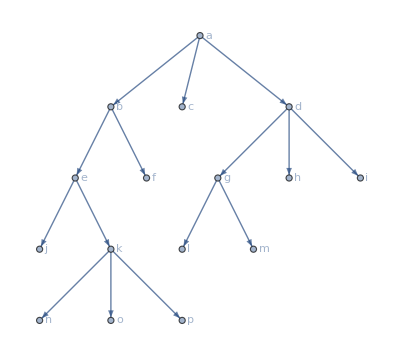

```mathematica
fig3Tree=orderedTree[{"a"->"b","a"->"c","a"->"d","b"->"e","b"->"f","d"->"g","d"->"h","d"->"i","e"->"j","e"->"k","g"->"l","g"->"m","k"->"n","k"->"o","k"->"p"},
<|"a"->0,"b"->1,"c"->2,"d"->3,"e"->1,"f"->2,"g"->1,"h"->2,"i"->3,"j"->1,"k"->2,"l"->1,"m"->2,"n"->1,"o"->2,"p"->3|>,VertexLabels->Placed["Name",After]]
```

### Subtrees

Before implementing the traversal algorithms, we need a function that determines a subtree of a tree. In particular, we want an function that, given a tree and a vertex, will return the subtree with the given vertex as the root and that includes all of its descendants.

To produce the subtree, we will use the Subgraph function and then copy the “order” attributes to the new tree from the original. The vertices that we want included in the subgraph are the given vertex, which will be the root of the subtree, together with all of its descendants. We begin by creating a function that finds all of the descendants of the given vertex. This function can apply to any rooted tree.

The approach is the same as we have used before. We begin with the given vertex and create a list consisting of its children, which we obtain with the findChildren function. We then begin a loop over the list of descendants. At each step, we add all of the children of the current vertex to the list, and then move on to the next vertex in the list. This continues until we reach the end of the list and there are no more children to add. (Note that this is referred to as a level-order traversal.)

```mathematica
descendants[T_?rootedTreeQ,parent_]:=Module[{dList,v,i},
dList=findChildren[T,parent];
i=1;
While[i≤Length[dList],
v=dList[[i]];
dList=Join[dList,findChildren[T,v]];
i++
];
dList
]
```

Compute the descendants of e in the example tree above.

```mathematica
descendants[fig3Tree,"e"]
```

{j,k,n,o,p}

To construct the subtree of an ordered rooted tree with a given vertex as its root, we need to: find the descendants of the given vertex; use the Subgraph function on the given vertex and all its descendants; copy the “order” attribute to the new tree; and set the “order” attribute of the root to 0.

```mathematica
subTree[T_?orderedRootedTreeQ,newRoot_,opts___]:=Module[{vList,subT,v},
vList=descendants[T,newRoot];
PrependTo[vList,newRoot];
subT=Subgraph[T,vList,opts];
Do[PropertyValue[{subT,v},"order"]=PropertyValue[{T,v},"order"]
,{v,vList}];
PropertyValue[{subT,newRoot},"order"]=0;
subT
]
```

We check this function by finding the subtree with root e and making sure it satisfies orderedRootedTreeQ.

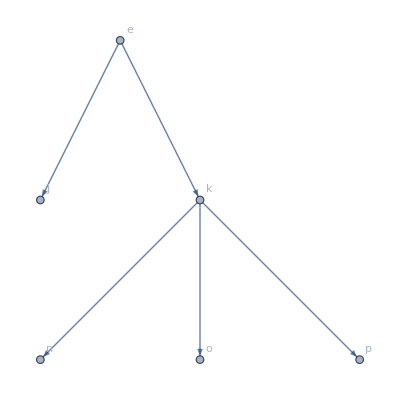

```mathematica
subExample=subTree[fig3Tree,"e",VertexLabels->"Name"]
```

```mathematica
orderedRootedTreeQ[subExample]
```

True

### Traversal Algorithms

We now implement the three traversal algorithms described in Section 11.3 of the textbook. We begin with the preorder traversal algorithm, which is given as Algorithm 1 in the text.

In the following, we use Reap and Sow in order to generate a list of the vertices in the order they are encountered. The result of Reap applied to an expression is a list whose first element is the result of the expression and whose second element is another list. This second list is itself a list of all the expressions that Sow had been applied to within the Reap expression. For example,

```mathematica
Reap[Sow[5];12;Sow[1+1];Sow[33];7]
```

{7,{{5,2,33}}}

The first element in the result is 7, since 7 is the result of the sequence of expressions inside the Reap. The second element in the result is a list of a list containing 5, 2, and 33, the values that were sown. The reason the second element of the main result is nested is because you can give Sow a second argument to “tag” certain results, which then are assembled into separate sublists.

```mathematica
Reap[Sow[5,"number"];12;Sow[1+1,"sum"];Sow[33,"number"];7]
```

{7,{{5,33},{2}}}

Here, we will not need the tagging feature. However, we will be using Sow recursively; that is, within the Reap we will apply Sow to a recursive call of the function. So it is the result of the recursive call to the function that will be sown. Therefore, before concluding the function, we want to extract the sown results, as illustrated below.

```mathematica
Reap[Sow[5];12;Sow[1+1];Sow[33];7][[2,1]]
```

{5,2,33}

#### Preorder

Given an ordered rooted tree, the preorder algorithm acts as follows. First, it prints the name of the root. Then, it calculates the children of the root and stores them in order. For each child, in order, the function recursively applies itself to the subtree with the given child as root.

```mathematica
preorder[T_?orderedRootedTreeQ]:=Module[{root,children,i,tempSubT},
Reap[
root=findRoot[T];
Sow[root];
children=findChildren[T,root];
children=Sort[children,(PropertyValue[{T,#1},"order"]<PropertyValue[{T,#2},"order"])&];
For[i=1,i≤Length[children],i++,
tempSubT=subTree[T,children[[i]]];
Sow[preorder[tempSubT]];
]
][[2,1]]
]
```

```mathematica
preorder[fig3Tree]
```

{a,{b,{e,{j},{k,{n},{o},{p}}},{f}},{c},{d,{g,{l},{m}},{h},{i}}}

The nesting of the lists in this output is indicative of the subtree structure. You can confirm that this output is consistent with the preorder traversal demonstrated in Figure 4 of Section 11.3 of the textbook. Applying Flatten will produce the list of vertices in the order they are visited.

```mathematica
Flatten@preorder[fig3Tree]
```

{a,b,e,j,k,n,o,p,f,c,d,g,l,m,h,i}

Finally, with this output, it is straightforward to create an animation that illustrates the traversal.

```mathematica
preorderAnimation[T_?orderedRootedTreeQ]:=Module[{traversal},
traversal=Flatten@preorder[T];
Animate[HighlightGraph[T,traversal[[1;;i]]],{{i,0,"step"},0,Length[traversal],1},AnimationRunning->False,AnimationRepetitions->1]
]
```

```mathematica
preorderAnimation[fig3Tree]
```

#### Postorder

Postorder traversal, described in Algorithm 3 of the text, is very similar to preorder traversal. The only change needed in the code is that, instead of printing the root at the start of the algorithm, the vertex is printed after the loop is completed.

```mathematica
postorder[T_?orderedRootedTreeQ]:=Module[{root,children,i,tempSubT},
Reap[
root=findRoot[T];
children=findChildren[T,root];
children=Sort[children,(PropertyValue[{T,#1},"order"]<PropertyValue[{T,#2},"order"])&];
For[i=1,i≤Length[children],i++,
tempSubT=subTree[T,children[[i]]];
Sow[postorder[tempSubT]];
];
Sow[root]
][[2,1]]
]
```

```mathematica
postorder[fig3Tree]
```

{{{{j},{{n},{o},{p},k},e},{f},b},{c},{{{l},{m},g},{h},{i},d},a}

#### Inorder

In inorder traversal, the algorithm first applies itself recursively to the first child of the vertex, then it prints the vertex, and then it applies itself to the remainder of the children, in order.

```mathematica
inorder[T_?orderedRootedTreeQ]:=Module[{root,children,i,tempSubT},
Reap[
root=findRoot[T];
children=findChildren[T,root];
children=Sort[children,(PropertyValue[{T,#1},"order"]<PropertyValue[{T,#2},"order"])&];
If[Length[children]≠0,
tempSubT=subTree[T,children[[1]]];
Sow[inorder[tempSubT]]
];
Sow[root];
For[i=2,i≤Length[children],i++,
tempSubT=subTree[T,children[[i]]];
Sow[inorder[tempSubT]];
]
][[2,1]]
]
```

```mathematica
inorder[fig3Tree]
```

{{{{j},e,{{n},k,{o},{p}}},b,{f}},a,{c},{{{l},g,{m}},d,{h},{i}}}

We leave it to the reader to create animations for inorder and postorder traversals.

### Infix Notation

In the remainder of this section, we discuss how to work with the infix, prefix, and postfix forms of arithmetic expressions, as described in Section 11.3 of the text. First, we will show how to create a tree representation of an infix expression. Then, we will explore how to evaluate expressions from their postfix and prefix forms.

Recall that infix notation is the usual notation for basic arithmetic and algebraic expressions. We will construct a function in the Wolfram Language that takes an infix expression and converts it into a tree representation. This tree representation can then be traversed using the traversals of the previous sections to form various arithmetic representation formats.

The algorithm we use to turn an arithmetic expression in infix notation into a tree is recursive. The basis case occurs when the expression consists of a single number or variable. In this case, the tree consists of a single vertex.

Otherwise, the expression consists of an operator, and two or more operands. In this case, we (1) apply the algorithm to the operands, and (2) combine the resulting trees with the operator as the common root. Implementing this will require some preliminary work.

First, we need to represent arithmetic expressions in the Wolfram Language in such a way that we can work with them and ensure that Mathematica will not evaluate them. This can be accomplished by applying Hold to the expression when entering it, as illustrated below.

```mathematica
Hold[2+3*5]
```

Hold[2+3 5]

Observe that FullForm reveals that associative operators, such as addition and multiplication, are treated as a single operation applied to more than two operands.

```mathematica
Hold[2*3*4*5]//FullForm
```

Hold[Times[2,3,4,5]]

For this reason, our expression trees will not be binary. For example, the product above would be represented by a tree with root Times and four children.

Second, we will need to be able to distinguish the basis case from the recursive case.

Third, the leaves in the tree will be numbers and variables and the internal vertices will be operations. In an expression like 3·4+7·(3+x), we have repetition among the operators and the operands (two 3’s, two additions, and two multiplications). We need to consider each of these to be a distinct object, since the Wolfram Language insists that the vertices in a graph be distinct. At the same time, we wish to display them with the same symbol in the tree.

Fourth, in the recursive step, we need to be able to identify the operator and separate the operands.

Fifth, we will need to implement a function to perform the combination of subtrees described in part (2) of the recursive step.

#### Distinguishing the Basis and Recursive Cases

Any arithmetic expression is either a single integer or variable, or it is two or more expressions joined by an arithmetic operator.

We can determine which kind it is by testing the head of the expression.

```mathematica
Head[5]
```

Integer

```mathematica
Head[x]
```

Symbol

However, observe that an expression such as 3+5 also reports having head Integer.

```mathematica
Head[3+5]
```

Integer

This is because Mathematica evaluates the arithmetic before apply the Head function. We will be using Hold to prevent arithmetic evaluation and algebraic simplification. However, with Hold in place, Head will identify the head of the expression as Hold.

```mathematica
Head[Hold[3+5]]
```

Hold

To obtain the correct head of an expression such as 3+5 while preventing evaluation, we use Part ([[…]]). Remember that 0 represents the head within a Part ([[…]]).

```mathematica
5[[0]]
```

Integer

For a held expression, [[1,0]] will give the head of the expression within the Hold. The 1 accesses the expression within the Hold, and then then 0 refers to the head of that expression.

```mathematica
Hold[3+5][[1,0]]
```

Plus

#### Ensuring That Each Occurrence of an Object Is Considered Distinct

The tree associated to the expression 3·4+7·(3+x) will have 9 vertices. The internal vertices, the operations, consist of two additions and two multiplications. The leaves, the numbers and variables, consist of 4, 7, x, and two 3s.

In a graph in the Wolfram Language, each vertex must be unique and distinct from all other vertices. In order to make Mathematica consider two 3s or two additions to be different, we will take advantage of the fact that a Module structure attaches an integer to each variable name in order to ensure it is unique. The following reveals the internal symbol associated to a local variable:

```mathematica
Module[{var},ToString[var]]
```

var$4534

To use this while building our expression tree, we will define an alternate version of newBinaryTree, which was defined earlier in the chapter. This new function, newExpressionTree, will declare a local variable and set it equal to the result of applying ToString to the variable. Since the local variable had not previously been assigned, this will store the internal representation of the variable. We then use that as the name of the vertex in a new tree. We set the VertexLabels property in order to have the graph displayed with the elements of the expression rather than the internal name.

```mathematica
newExpressionTree[r_,opts___]:=Module[{T,v},
v=ToString[v];
T=orderedTree[{v},{},<|v->0|>,opts];
PropertyValue[{T,v},VertexLabels]=Placed[r,Below];
T
]
```

#### Identifying the Operator and Operands

In the recursive case, we must separate a complex expression into its operator and operands. Consider the following example:

```mathematica
exampleExpr=Hold[3*4+7*(3+x)]
```

Hold[3 4+7 (3+x)]

This expression, 3·4+7·(3+x) consists of the sum of 3·4 and 7·(3+x). We will obtain these two operands by applying Extract.

Extract is similar to Part ([[…]]) or Take in that it returns a part of an expression. However, it allows an optional third argument to apply a head to the part of the expression before it is returned. This is important here because we need to prevent Mathematica from simplifying the operands.

The arguments to Extract will be the expression, the part specification, and Hold. To see what the part specification should be, look at the full form of exampleExpr.

```mathematica
FullForm[exampleExpr]
```

Hold[Plus[Times[3,4],Times[7,Plus[3,x]]]]

We see that the expression is entirely enclosed in Hold, so part specification {1} will refer to the entire algebraic expression, which has head Plus. The arguments of the top Plus are then referenced as {1,1} and {1,2}.

```mathematica
Extract[exampleExpr,{1,1},Hold]
```

Hold[3 4]

```mathematica
Extract[exampleExpr,{1,2},Hold]
```

Hold[7 (3+x)]

We can obtain a list of both operands by giving a list of part specifications as the second argument.

```mathematica
Extract[exampleExpr,{{1,1},{1,2}},Hold]
```

{Hold[3 4],Hold[7 (3+x)]}

Since associative operations may have more than two operands, we need to determine the number of operands. Consider the example below.

```mathematica
exampleExpr2=Hold[5x+12+7]
```

Hold[5 x+12+7]

```mathematica
FullForm[exampleExpr2]
```

Hold[Plus[Times[5,x],12,7]]

To determine the number of operands of the Plus, we will replace the main operator with the List head. Using the Apply operator at level 1 (@@@) will leave the Hold in place.

```mathematica
List@@@exampleExpr2//FullForm
```

Hold[List[Times[5,x],12,7]]

We can then release the hold and determine the length of the list.

```mathematica
Length[ReleaseHold[List@@@exampleExpr2]]
```

3

Which then helps us create the appropriate list of part specifications to use with Extract.

```mathematica
Extract[exampleExpr2,Table[{1,i},{i,3}],Hold]
```

{Hold[5 x],Hold[12],Hold[7]}

Note that we can use {1,0} to obtain the head of the expression, that is, the operator. This is equivalent to the use of Part ([[…]]) described above for the same purpose.

```mathematica
Extract[exampleExpr,{1,0}]
```

Plus

```mathematica
exampleExpr[[1,0]]
```

Plus

#### Combining Subtrees

As part of Huffman coding in Section 2, we wrote a function, joinHTrees, for joining two existing trees at a new root. We create a version of that function here.

The most important difference in this version of the function is that it joins ordered trees that are not necessary binary. As a result, it needs to be able to accept more than two trees, so the second argument will be a list of ordered rooted trees. The other differences between this and the earlier function amount to looping over the elements of the list of trees, rather than acting on the two arguments separately.

One element of this function worth commenting on is the use of Sequence together with the Apply (@@) operator. The Sequence head refers to a comma-separated sequence of expressions not contained in a List or other structure. In this function, the goal is to strip away the outer List from the the result of Table so that elements produced by the Table can be combined with other objects within a Join.

```mathematica
joinTrees[newR_,trees:{__?orderedRootedTreeQ},opts___]:=Module[{newRI,A,newVerts,oldRoots,Aroot,newEdges,newOrders,newT,v,e,p,w},
newRI=ToString[newRI];
newVerts=Join[{newRI},Sequence@@Table[VertexList[A],{A,trees}],1];
oldRoots=Table[findRoot[A],{A,trees}];
newEdges=Join[Sequence@@Table[EdgeList[A],{A,trees}],Table[DirectedEdge[newRI,Aroot],{Aroot,oldRoots}]];
newOrders=Join[Sequence@@Flatten[Table[orderAssociation[A],{A,trees}],1],Association@@Table[oldRoots[[i]]->i,{i,Length[oldRoots]}],<|newRI->0|>];
newT=orderedTree[newVerts,newEdges,newOrders,opts];
Do[PropertyValue[{newT,v},VertexLabels]=PropertyValue[{A,v},VertexLabels]
,{A,trees},{v,VertexList[A]}];
PropertyValue[{newT,newRI},VertexLabels]=Placed[newR,After];
newT
]
```

#### The Main Function

With joinTrees and newExpressionTree prepared, we are ready to write the function for turning infix expressions into binary trees.

The function accepts a single argument, expr, the expression. We will give the function the HoldFirst attribute, so that the expression will be held without our having to explicitly type Hold when executing the function. This holds the argument only until it is first evaluated, so we must immediately place a more permanent Hold on it, provided it was not already explicitly held, and assign it to e.

We first test the type of e. If it is an integer or a symbol, then we use newExpressionTree to create a new binary tree with e as the only vertex.

Otherwise, we are in the recursive case. We use Extract to determine the operands and the operator. After recursive calls to the function to create the trees for the operands, the subtrees are joined at the operator into the result tree.

Here is the function.

```mathematica
SetAttributes[expressionTree,HoldFirst];
expressionTree[expr_,opts___]:=Module[{e,operator,len,operands,trees,op,result},
If[expr[[0]]===Hold,
e=expr,
e=Hold[expr]
];
If[e[[1,0]]===Integer||e[[1,0]]===Symbol,
result=newExpressionTree[ReleaseHold[e],opts],
operator=Extract[e,{1,0}];
len=Length[ReleaseHold[List@@@e]];
operands=Extract[e,Table[{1,i},{i,len}],Hold];
trees=Table[expressionTree[op],{op,operands}];
result=joinTrees[operator,trees,opts]
];
result
]
```

We test the function on the example expression.

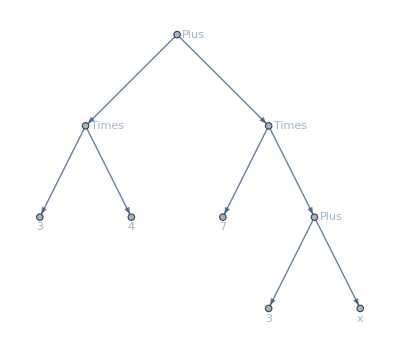

```mathematica
exampleTree=expressionTree[3*4+7*(3+x)]
```

Observe that when an associative operation is used without parentheses, like addition in the example below, the expression tree respects the associativity.

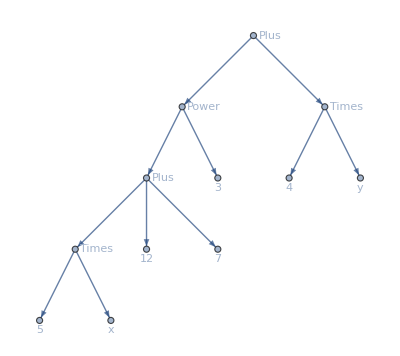

```mathematica
expressionTree[(5x+12+7)^3+4 y]
```

We may also wish to apply expressionTree to a symbol that has been assigned to an expression. Since HoldFirst will not allow the symbol to resolve to the stored expression, we provide a specific definition for expressionTree applied to a symbol. We use Evaluate to resolve the symbol. If the symbol evaluates to an expression, we pass that to the main expressionTree.

```mathematica
expressionTree[s_Symbol,opts___]:=If[Head[Evaluate[s]]=!=Symbol,expressionTree[Evaluate[s],opts],newExpressionTree[s,opts]]
```

### Prefix and Postfix Notation

Suppose we are given a tree representation of an arithmetic expression. We can express these trees in postfix, infix, or prefix form by applying the respective traversal algorithm we designed above. For example, our animation function for preorder traversal illustrates the order in which Example 6 from the main text would be written in prefix notation.

```mathematica
preorderAnimation[expressionTree[(x+y)^2+(x-4)/3]]
```

Note that the Wolfram Language interprets division as multiplication by the reciprocal. If you prefer the tree to include division, you can explicitly include the Divide function.

```mathematica
preorderAnimation[expressionTree[(x+y)^2+Divide[x-4,3]]]
```

It is left to the reader to make the necessary functions to output infix, prefix, and postfix expressions. Keep in mind that the integers, variables, and operators are stored as the VertexLabels property of the vertices of the tree, not as the vertices themselves.

As a final example in this section, we demonstrate how to evaluate a given postfix expression. We will represent the postfix expression as a list of symbols, each of which is either a number or one of the arithmetic operations’ symbols as a string.

Since we are considering postfix expressions, we read the list of symbols from left to right. Each time we encounter an operation, that operation is applied to the previous two numbers and we update the list by replacing the two numbers and the operation symbol by the result of the operation.

```mathematica
evalPostfix[expr_List]:=Module[{i,L},
L=expr;
While[Length[L]>1,
i=1;
While[FreeQ[{"+","-","*","/","^"},L[[i]]],i++];
Switch[L[[i]],
"+",L[[i]]=L[[i-2]]+L[[i-1]],
"-",L[[i]]=L[[i-2]]-L[[i-1]],
"*",L[[i]]=L[[i-2]]*L[[i-1]],
"/",L[[i]]=L[[i-2]]/L[[i-1]],
"^",L[[i]]=L[[i-2]]^L[[i-1]]];
L=Drop[L,{i-2,i-1}]
];
L[[1]]
]
```

Note that the Drop function removes a range of elements of the list.

```mathematica
postfixExample={7,2,3,"*","-",4,"^",9,3,"/","+"}
```

{7,2,3,*,-,4,^,9,3,/,+}

```mathematica
evalPostfix[postfixExample]
```

4

The reader is left to explore evaluation in the prefix case, which requires only a simple modification.

## 11.4 Spanning Trees

This section explains how to use Mathematica to construct spanning trees for graphs and how to use spanning trees to solve many different types of problems. Spanning trees have a myriad of applications, including coloring graphs, placing n queens on a n×n chessboard so that no two of the queens attack each other, and finding a subset of a set of numbers with a specified sum. All of these problems, which are described in detail in the text, will be explored computationally in this section. First, we will show how to form spanning trees using two algorithms: depth-first search and breadth-first search. Then, we will solve the problems just mentioned.

The Wolfram Language includes two functions, DepthFirstScan and BreadthFirstScan that will perform a search on a graph. Both functions accept a Graph and a vertex of the graph as the first two arguments. With these two arguments, the functions will return a list of vertices, say {v_1,v_2,…,v_n}. Suppose that the VertexList function returns {u_1,u_2,…,u_n}. Then, the output of DepthFirstScan or BreadthFirstScan indicates that the tree whose edges are v_i->u_i is a spanning tree of the graph, with root the vertex such that u_i=v_i.

The function TreeGraph can be used to form a tree from the output of DepthFirstScan or BreadthFirstScan. TreeGraph can accept as input two lists of vertices, where the first is the list of all vertices to appear in the tree and the second is the list each of whose elements is the predecessor of the corresponding element of the first list. A simple example is shown below of a tree with root 2, vertices 1 and 3 are the children of 2, and 4 and 5 are the children of 3, and vertex 6 is the child of 1.

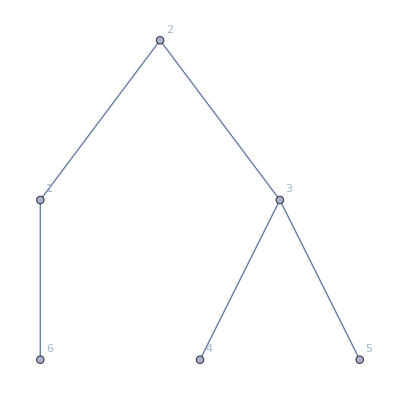

```mathematica
TreeGraph[{1,2,3,4,5,6},{2,2,2,3,3,1},VertexLabels->"Name"]
```

We will illustrate the use of DepthFirstScan or BreadthFirstScan with the graph from Exercise 13 of Section 11.4, which we recreate.

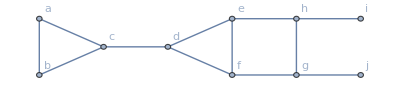

```mathematica
exercise13=Graph[{"a","b","c","d","e","f","g","h","i","j"},{"a"->"b","a"->"c","b"->"c","c"->"d","d"->"e","d"->"f","e"->"f","e"->"h","f"->"g","g"->"h","g"->"j","h"->"i"},DirectedEdges->False,VertexCoordinates->{{0,1},{0,0},{1,0.5},{2,0.5},{3,1},{3,0},{4,0},{4,1},{5,1},{5,0}},VertexLabels->"Name"]
```

Using DepthFirstScan and passing the output to TreeGraph allows us to draw the spanning tree obtained by a depth-first search.

```mathematica
exercise13DepthFirst=DepthFirstScan[exercise13,"a"]
```

{a,a,b,c,d,e,f,g,h,g}

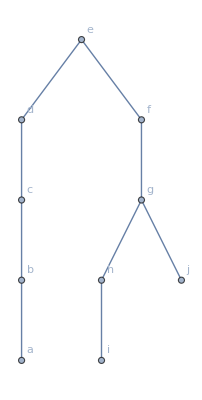

```mathematica
TreeGraph[VertexList[exercise13],exercise13DepthFirst,VertexLabels->"Name"]
```

Observe that BreadthFirstScan produces a different tree.

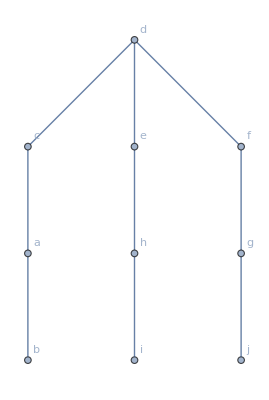

```mathematica
TreeGraph[VertexList[exercise13],BreadthFirstScan[exercise13,"a"],VertexLabels->"Name"]
```

Note that in both cases, the initial vertex, a, is not drawn at the root of the tree. As we described previously, Mathematica draws trees to minimize depth, irrespective of the logical root. As before, we can specify the root by using the GraphLayout option.

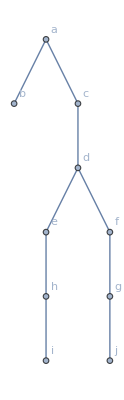

```mathematica
TreeGraph[VertexList[exercise13],BreadthFirstScan[exercise13,"a"],VertexLabels->"Name",GraphLayout->{"LayeredEmbedding","RootVertex"->"a"}]
```

DepthFirstScan and BreadthFirstScan both accept an optional third argument, which is given as a list of rules. The rules in the list identify an “event” with a pure Function (&) to be executed when the event occurs. We will illustrate this by highlighting the BreadthFirstScan tree within the graph. We make a copy of the graph first, since our execution of BreadthFirstScan will modify the graph.

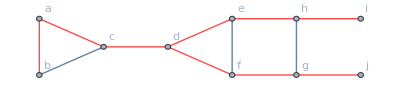

```mathematica
exercise13Copy=exercise13;
BreadthFirstScan[exercise13Copy,"a",{"FrontierEdge"->((PropertyValue[{exercise13Copy,#},EdgeStyle]=Directive[Thick,Red])&)}]; exercise13Copy
```

Let us explain the above in more detail. BreadthFirstScan is called on the graph exercise13Copy and told to start with vertex a. The third argument is the list containing a single Rule (->) identifying the event “FrontierEdge” with a pure Function (&). A frontier edge refers to an edge between a vertex that is currently being visited and a vertex that is newly discovered as a result of visiting the current vertex. The pure Function (&) associated to the event “FrontierEdge” is called with a single argument, the edge in question. In this example, we use the function to highlight the edges which are traversed by the breadth-first exploration.

Alternatively, we could use Sow and Reap to obtain a list of the edges in the order they are followed. Note that Sow accepts a single argument so it is not necessary to explicitly call it on a Slot (#).

```mathematica
exercise13breadthList=Reap[BreadthFirstScan[exercise13,"a",{"FrontierEdge"->Sow}]][[2,1]]
```

{a<->b,a<->c,c<->d,d<->e,d<->f,e<->h,f<->g,h<->i,g<->j}

We can now use this list to create an animation.

```mathematica
Animate[HighlightGraph[exercise13,exercise13breadthList[[1;;i]]],{{i,0,"step"},0,Length[exercise13breadthList],1},AnimationRunning->False,AnimationRepetitions->1]
```

We leave it to the reader to create a function that generates such an animation automatically.

A second useful event that can be used with DepthFirstScan and BreadthFirstScan is “DiscoverVertex”. This event occurs when a vertex is discovered for the first time. The associated function is called with up to three arguments: the vertex being discovered, the vertex currently being visited, and the distance the visited vertex is from the starting vertex.

The interested reader is encouraged to consult the help pages for DepthFirstScan or BreadthFirstScan for information on other events that can be used.

Despite the Wolfram Language’s existing functions, we will develop our own using depth-first and breadth-first search functions as a way to illustrate these important algorithms.

### Depth-First Search

We begin by implementing depth-first search. As the name of the algorithm suggests, vertices are visited in order of increasing depth of the spanning tree. Our implementation is based on Algorithm 1 of Section 11.4 of the textbook.

Recall the terminology defined in the textbook. We say that we are “exploring a vertex” v from the time the vertex is first added to the spanning tree until we have backtracked back to v for the last time. Note that at any step in the process, we are generally exploring multiple vertices. In particular, the root of the spanning tree starts being explored at the very beginning of the process and continues being explored until it terminates.

The function, which we call depthSearch, will take two arguments: an undirected graph and a vertex in that graph. The function operates as follows:

First, we check that the graph is connected using the Wolfram Language’s ConnectedGraphQ function. If not, there can be no spanning tree and the function returns $Failed.

Next, we initialize the following variables:

toVisit will be the set of vertices of the graph that have not yet been visited. It is initialized to the set of vertices of the graph minus the initial vertex.

exploring will be the list of vertices that are currently being explored. As vertices are visited, they are added to the end of the exploring list. When a vertex has been fully explored, that is, when it has no neighbors not already visited, then we remove it from the exploring list. exploring is initialized to the vertex that is given as the second argument.

T will be the spanning tree that is constructed. It is initialized to the graph consisting of all the vertices of the graph, but with no edges. Provided that the graph is connected, we know that all the vertices will appear in T and this saves us from adding them one at a time.

Following initialization, we begin a While loop which terminates when the exploring list is empty. The variable v is set to the last element of the exploring list. We then compute the intersection, N, of the neighbors of v and the toVisit set of vertices not already contained in the tree. Either,

N is non-empty, in which case, one of its elements is chosen as w, the next vertex to visit. The edge v->w is added to the tree T. In addition, w is removed from the toVisit set and added to the end of the exploring list. In the next iteration of the While loop, this new vertex will be set to be v.

N is empty, in which case the vertex v has been explored completely and so it can be removed from the exploring list. The next iteration of the While loop will set v to be the vertex one step back in the exploring list. This is the “backtracking” step.

Here, now, is the function.

```mathematica
depthSearch[G_?UndirectedGraphQ,startV_,opts___]:=Module[{toVisit,exploring,T,v,N,w},
If[!ConnectedGraphQ[G],Return[$Failed]];
toVisit=Complement[VertexList[G],{startV}];
exploring={startV};
T=Graph[VertexList[G],{},opts];
While[Length[exploring]>0,
v=exploring[[-1]];
N=Intersection[AdjacencyList[G,v],toVisit];
If[Length[N]>0,
w=N[[1]];
T=EdgeAdd[T,DirectedEdge[v,w]];
toVisit=Complement[toVisit,{w}];
AppendTo[exploring,w],
(*else*)
exploring=Delete[exploring,-1]
]
];
T
]
```

We test this with our Exercise 13 example from above.

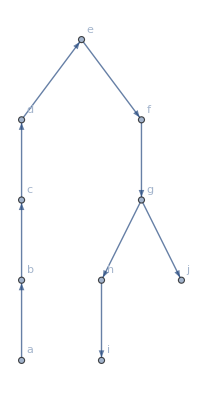

```mathematica
depthSearch[exercise13,"a",VertexLabels->"Name"]
```

We can reposition the vertices to match the original by setting VertexCoordinates to the result of GraphEmbedding applied to the original graph.

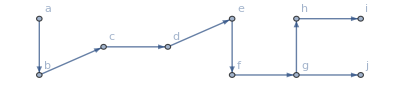

```mathematica
depthSearch[exercise13,"a",VertexLabels->"Name",VertexCoordinates->GraphEmbedding[exercise13]]
```

We can also use HighlightGraph to highlight the spanning tree relative to the original graph. However, since our function generates directed edges and the original graph was undirected, we need to use UndirectedGraph to convert the edges of the spanning tree back to undirected edges.

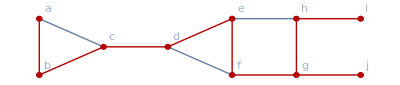

```mathematica
HighlightGraph[exercise13,UndirectedGraph[depthSearch[exercise13,"a"]]]
```

### Breadth-First Search

We now turn to an implementation of a breadth-first search. Recall that the breadth-first algorithm works by examining all vertices at the current depth of the spanning tree before moving on to the next level of the graph. Our implementation will follow Algorithm 2 of Section 11.4 of the text.

The function, to be called breadthSearch, again takes two arguments: an undirected graph and a vertex to act as the starting point. It proceeds as follows:

First, we check that the graph is connected using the Wolfram Language’s ConnectedGraphQ function.

Next, we initialize the following variables:

toVisit, as before, will be the set of vertices of the graph not yet visited. It is initialized to the set of vertices of the graph with the initial vertex excluded.

toProcess will be the list of vertices that have been determined to be incident to a vertex in the tree but which have not yet been processed. toProcess is initialized to the vertex that is given as the second argument to the procedure.

T will be the spanning tree that is constructed. Once again, it is initialized to the tree consisting of all the vertices of the given graph, but with no edges.

Following initialization, we begin a While loop that terminates when the toProcess list is empty. The variable v is set to the first element of the toProcess list. We then compute the intersection, N, of the neighbors of v and the toVisit set. For each element w of N, an edge v->w is added to T and w is added to the end of the toProcess list and removed from the toVisit set. Then, v is removed from toProcess.

Observe that, since neighbors are added to the end of the toProcess list and are processed from the beginning of the list, we are assured that all vertices on a given level will be processed before any vertex at a lower level.

Here is the implementation.

```mathematica
breadthSearch[G_?UndirectedGraphQ,startV_,opts___]:=Module[{toVisit,toProcess,T,v,N,w},
If[!ConnectedGraphQ[G],Return[$Failed]];
toVisit=Complement[VertexList[G],{startV}];
toProcess={startV};
T=Graph[VertexList[G],{},opts];
While[Length[toProcess]>0,
v=toProcess[[1]];
N=Intersection[AdjacencyList[G,v],toVisit];
Do[
T=EdgeAdd[T,v->w];
AppendTo[toProcess,w];
toVisit=Complement[toVisit,{w}];
,{w,N}];
toProcess=Delete[toProcess,1];
];
T
]
```

Once again, we illustrate using Exercise 13.

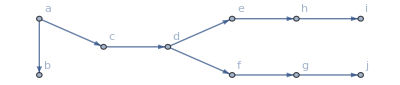

```mathematica
breadthSearch[exercise13,"a",VertexLabels->"Name",VertexCoordinates->GraphEmbedding[exercise13]]
```

Before moving on to backtracking, we take a moment to compare the trees produced by the two algorithms.

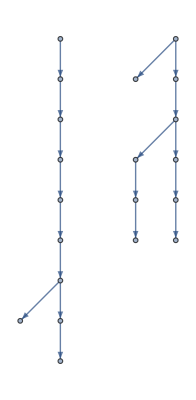

```mathematica
GraphDisjointUnion[breadthSearch[exercise13,"a"],depthSearch[exercise13,"a"],GraphLayout->"LayeredDigraphEmbedding"]
```

Notice that the two spanning trees are quite different. In particular, the depth-first search has a deep and thin structure, whereas the breadth-first search is shorter and wider.

### Graph Coloring via Backtracking

Backtracking is a method that can be used to find solutions to problems that might be impractical to solve using exhaustive search techniques. Backtracking is based on the systematic search for a solution to a problem using a decision tree. (See the text for a complete discussion.) Here, we show how to use backtracking to solve several different problems, including coloring a graph, the n-queens problem, and the subset sum problem.

The first problem we will attack via a backtracking procedure is the problem of coloring a graph using n colors, where n is a positive integer. Given a graph, we will attempt to color it using n colors using the method described in Example 6 of Section 11.4.

Fix an order on the vertices of the graph, say v_1,v_2,…,v_m and fix an ordering of the colors as color 1, color 2, ..., color n. We will use the ordering of the vertices that Mathematica automatically imposes. For the colors, we will require an ordered list of colors as one of the arguments to the function.

We store the current state of the coloring in a list we will call coloring. The ith entry in this list will correspond to the color of the ith vertex. For example, coloring = {1,2,1}, corresponds to vertex v_1 assigned color 1, vertex v_2 assigned color 2, and vertex v_3 assigned color 1. This coloring list is similar to the exploring list from depthSearch. In both cases, you can think of the list as storing the path from the root of the tree to the current vertex. In this case, the level, which corresponds to the position in the list, carries additional information. Specifically, level k in the decision tree (i.e., position k in the coloring list) corresponds to deciding the color of vertex v_k.

We initialize coloring to {1} and set a counter variable i to 2. The variable i will indicate the vertex that requires a decision.

Set N equal to the neighbors of the ith vertex of the graph, and then construct a set, used, consisting of the indices of the colors assigned to the neighbors. The ith vertex will be assigned the color with the smallest index not in used, assuming there are any remaining colors.

If there are no possible colors for the ith vertex, then we must backtrack. We decrease i by one. To ensure that we do not repeat a choice already made when we revisit a vertex, we make the following modification to how colors are chosen. If the ith position of coloring has already been set, then we know we are in the process of backtracking. We insist that the new choice for the color of vertex i is the smallest possible color greater than the current color.

The function terminates in one of two cases. If i is set to a value greater than the number of vertices, then we know that coloring contains a valid assignment for all vertices. On the other hand, if i is ever set to 1, then we know that we have backtracked all the way to the root. Since the color of the first vertex does not affect the validity of the coloring, this indicates that we have exhausted all possible colorings and that the graph cannot be colored with n colors.

Our function will be called backColor. It will accept two arguments: the graph to be colored and a list of colors. If it is successful, it will display the graph with the vertices colored. If it determines that there is no n-coloring of the graph, it will return $Failed.

```mathematica
backColor[G_Graph,C_List]:=Module[{verts,numverts,allcolorsL,k,coloring,i,N,j,used,available,g},
verts=VertexList[G];
numverts=Length[verts];
allcolorsL=Range[Length[C]];
coloring={1};
i=2;
While[i>1&&i≤numverts,
N=VertexList[NeighborhoodGraph[G,verts[[i]]]];
used={};
For[j=1,j≤i-1,j++,
If[MemberQ[N,verts[[j]]],AppendTo[used,coloring[[j]]]];
];
If[Length[coloring]≥i,used=Union[used,Range[coloring[[i]]]]];
available=Complement[allcolorsL,used];
If[Length[available]>0,
coloring=Append[coloring[[1;;i-1]],First[available]];
i++,
(*else*)
If[Length[coloring]≥i,coloring=coloring[[1;;i-1]]];
i--
]
];
If[i>numverts,
g=G;
For[k=1,k≤numverts,k++,
PropertyValue[{g,verts[[k]]},VertexStyle]=C[[coloring[[k]]]]
];
Return[g],
(*else*)
Return[$Failed]
]
]
```

We test our function on the example given in Figure 11 of Section 11.4 of the main text.

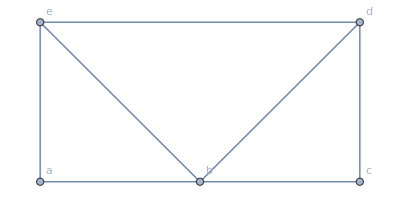

```mathematica
figure11Graph=Graph[{"a","b","c","d","e"},{"a"->"b","a"->"e","b"->"c","b"->"d","b"->"e","c"->"d","d"->"e"},DirectedEdges->False,VertexCoordinates->{{0,0},{1,0},{2,0},{2,1},{0,1}},VertexLabels->"Name"]
```

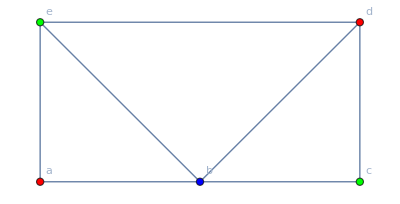

```mathematica
backColor[figure11Graph,{Red,Blue,Green}]
```

On the other hand, the complete graph on 5 vertices cannot be 3- or 4-colored. Here, instead of specifying the colors by symbol, we obtain them from ColorData.

```mathematica
K5=CompleteGraph[5];
```

```mathematica
backColor[K5,Table[ColorData[63][i],{i,3}]]
```

$Failed

```mathematica
backColor[K5,Table[ColorData[63][i],{i,4}]]
```

$Failed

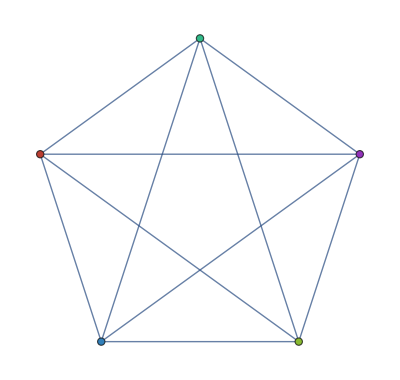

```mathematica
backColor[K5,Table[ColorData[63][i],{i,5}]]
```

Before moving on to the n-queens problem, we illustrate how we can modify our backtracking function to record and display the decision tree. Instead of displaying the graph, our modified algorithm will produce the decision tree. We do this by building a list of the decisions. Each time a color is assigned, we create a new vertex by adding the current state of the coloring list (converted to a string) and connecting it to the previous state.

```mathematica
backColorDT[G_Graph,C_List]:=Module[{verts,numverts,allcolorsL,k,coloring,i,N,j,used,available,DTList,parentV,newV},
verts=VertexList[G];
numverts=Length[verts];
allcolorsL=Range[Length[C]];
coloring={1};
newV=ToString[coloring];
DTList={};
i=2;
While[i>1&&i≤numverts,
N=VertexList[NeighborhoodGraph[G,verts[[i]]]];
used={};
For[j=1,j≤i-1,j++,
If[MemberQ[N,verts[[j]]],AppendTo[used,coloring[[j]]]];
];
If[Length[coloring]≥i,used=Union[used,Range[coloring[[i]]]]];
available=Complement[allcolorsL,used];
If[Length[available]>0,
parentV=ToString[coloring[[1;;i-1]]];
coloring=Append[coloring[[1;;i-1]],First[available]];
newV=ToString[coloring];
AppendTo[DTList,parentV->newV];
i++,
(*else*)
If[Length[coloring]≥i,coloring=coloring[[1;;i-1]]];
i--
]
];
Graph[DTList,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
]
```

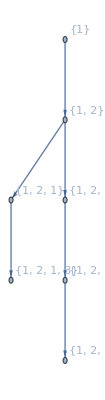

```mathematica
backColorDT[figure11Graph,{Red,Blue,Green}]
```

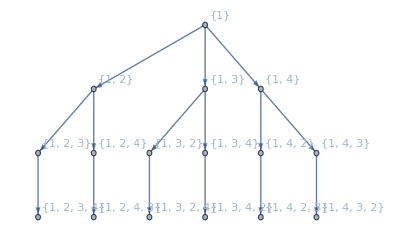

```mathematica
backColorDT[K5,Table[ColorData[63][i],{i,4}]]
```

### n-Queens Problem via Backtracking

Another problem with an elegant backtracking solution is the problem of placing n queens on an n×n chessboard so that no queen can attack another. This means that no two queens can be placed on the same horizontal, vertical, or diagonal line. We will solve this problem with a backtracking algorithm. The solution we present here is based on the solution given in Example 7 in Section 11.4. We place queens in a greedy fashion on the chessboard until either all the queens are placed or there is no available position for a queen to be placed without coming under attack from a queen already on the board.

Following the textbook, the ith step in the backtracking algorithm will be to place a queen in the ith column (or file, in chess terms). Like the coloring list and exploring list, the algorithm will build a queens list. In this case, queens[[i]]=j will indicate that a queen is placed in the jth row (rank) in the ith column (file). We will build a helper function, validQueens, that, given the dimension of the board and the current queens list, will determine the possible locations for a queen in the next column.

To implement validQueens, we will need a representation of the status of the board; specifically, for each square on the board, whether it is safe or under attack. It is natural to represent the board as a matrix with an entry 1 indicating that the corresponding square is safe and 0 that it is under attack. We create a square matrix with all entries initialized to 1 by issuing the ConstantArray function with two arguments: the common value 1 and the dimension of the matrix in a list. For example, the following initializes the matrix representing the board of dimension 5 on which no queens have been placed.

```mathematica
ConstantArray[1,{5,5}]//MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1)

We now create a boardStatus function that, given the current list of queen locations and the dimension of the board, will return a matrix representing the board with that configuration. The matrix will contain 1 in positions not under attack, 0 in positions under attack, and will represent the location of queens by the symbol Q.

```mathematica
boardStatus[queenList_List,dim_Integer]:=Module[{board,i,dif,qRank,qFile,vQueens},
board=ConstantArray[1,{dim,dim}];
For[qFile=1,qFile≤Length[queenList],qFile++,
qRank=queenList[[qFile]];
For[i=1,i≤dim,i++,
board[[qRank,i]]=0;
board[[i,qFile]]=0;
dif=i-qFile;
If[qRank+dif≤dim&&qRank+dif≥1,board[[qRank+dif,i]]=0];
If[qRank-dif≤dim&&qRank-dif≥1,board[[qRank-dif,i]]=0]
]
];
For[qFile=1,qFile≤Length[queenList],qFile++,
board[[queenList[[qFile]],qFile]]="Q"
];
board
]
```

For example, on a 10×10 board, with the first queen in the second row and the second queen in the seventh row, the board looks as follows.

```mathematica
boardStatus[{2,7},10]//MatrixForm
```

(0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
Q | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
0 | Q | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1)

The validQueens function will take the same arguments, the list of queen locations and dimension of the board, pass them to boardStatus, and use the resulting matrix to determine available positions in the next column. We could omit the boardStatus function and instead create validQueens independently, but, as you see above, the boardStatus function provides a useful visualization.

```mathematica
validQueens[queenList_List,dim_Integer]:=Module[{board,file,i,freeSet},
board=boardStatus[queenList,dim];
file=Length[queenList]+1;
freeSet={};
For[i=1,i≤dim,i++,
If[board[[i,file]]==1,AppendTo[freeSet,i]]
];
freeSet
]
```

With this preliminary work out of the way, we are ready to write the main program, nQueens. It will work in much the same way as our previous examples.

We keep a queens list, initialized to the empty list, that records the locations of queens.

We initialize a counter file to 1. This indicates the column in which we need to place a queen. Notice that, in the backColor algorithm, we initialized the counter to 2. The reason for the difference is that, in the coloring algorithm, the color of the first vertex was arbitrary and changing it from color 1 to a different color could not possibly affect the outcome. In this problem, it may be the case that there is no solution with the first queen in file 1, rank 1, but there is a solution if the file 1 queen is in a different rank.

Apply the validQueens function with the queens list and the board dimension. Store the resulting set as open.

As with the backColor algorithm, we determine if the current assignment is a new assignment or a result of backtracking. If it is a backtracking step, we remove from open the positions equal to or smaller than the previous attempt.

We terminate when file either exceeds the board dimension, in which case we have found a solution, or when it is backtracked to 0, in which case we have exhausted all possibilities.

```mathematica
nQueens[boardDim_Integer]/;boardDim>0:=Module[{queens={},file=1,open,i},
While[file>0&&file≤boardDim,
open=validQueens[queens[[1;;file-1]],boardDim];
If[Length[queens]≥file,
open=Complement[open,Range[queens[[file]]]]];
If[open≠{},
queens=Join[queens[[1;;file-1]],{open[[1]]}];
file++,
(*else backtrack*)
queens=queens[[1;;file-1]];
file--
]
];
If[file>boardDim,
Return[MatrixForm[boardStatus[queens,boardDim]]],
Return[$Failed]
]
]
```

We can use this to find one solution to the 8-queens problem (8×8 is the size of the standard board).

```mathematica
nQueens[8]
```

(Q | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Q | 0
0 | 0 | 0 | 0 | Q | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Q
0 | Q | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Q | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Q | 0 | 0
0 | 0 | Q | 0 | 0 | 0 | 0 | 0)

### Subset Sum Problem via Backtracking

Finally, we consider the subset sum problem. Given a set of integers S and a value M, we want to find a subset B of S whose sum is M. To use backtracking on this problem, we first impose an ordering on the set S. We successively select integers from S to include in B until the sum of the elements of B equals or exceeds M, and backtrack when the sum exceeds M.

Before we get to the main algorithm, it is worth reviewing two items of syntax. First, given a list of values, we can compute their sum with the Plus function using Apply (@@) to replace the List head with the Plus head, which then results in the sum being computed.

```mathematica
listofvalues={3,7,11,15,-4}
```

{3,7,11,15,-4}

```mathematica
Plus@@listofvalues
```

32

Second, given a list of values and a second list consisting of indices into the first list, we can obtain the sublist of values corresponding to the positions described by the second list by using the Part ([[…]]) operator with the list of indices.

```mathematica
listofstuff={"a","b","c","d","e","f","g"}
```

{a,b,c,d,e,f,g}

```mathematica
listofindices={1,3,4,7}
```

{1,3,4,7}

```mathematica
listofstuff[[listofindices]]
```

{a,c,d,g}

```mathematica
listofstuff[[{3,4,6}]]
```

{c,d,f}

As the general pattern of backtracking algorithms should be clear by this point, we omit a detailed description of the function.

```mathematica
subsetSum[S:{__Integer},M_Integer]:=Module[{bIndices,allIndices,i,availIndices,k,currentSum},
bIndices={};
allIndices=Range[Length[S]];
i=1;
currentSum=0;
While[i>0&&currentSum≠M,
availIndices=Complement[allIndices,bIndices];
If[Length[bIndices]≥i,availIndices=Complement[availIndices,Range[bIndices[[i]]]]];
Do[If[currentSum+S[[k]]>M,availIndices=Complement[availIndices,{k}]]
,{k,availIndices}];
If[availIndices≠{},
bIndices=Append[bIndices[[1;;i-1]],availIndices[[1]]];
i++,
(*else*)
If[Length[bIndices]≥i,bIndices=bIndices[[1;;i-1]]];
i--
];
currentSum=Plus@@S[[bIndices[[1;;i-1]]]]
];
If[i==0,
Return[$Failed],
Return[S[[bIndices]]]
]
]
```

```mathematica
subsetSum[{31,27,15,11,7,5},39]
```

{27,7,5}

```mathematica
subsetSum[{31,27,15,11,7,5},40]
```

$Failed

## 11.5 Minimum Spanning Trees

This section explains how to use Mathematica to find the minimum spanning tree of a weighted graph. Recall that a minimum spanning tree T of a weighted graph G is a spanning tree of G with the minimum weight of all spanning trees of G. The two best known algorithms for constructing minimum spanning trees are called Prim’s algorithm and Kruskal’s algorithm. In this section, we will implement these algorithms, as this is another case in which understanding the implementation can help you better understand the algorithms.

Before implementing the algorithms and finding minimum spanning trees, though, we will describe two built-in Wolfram Language functions, GraphDistance and GraphDistanceMatrix, that calculate the minimum distance between two vertices in a graph.

First, we construct a graph to use as an example. We will recreate Exercise 3 from Section 11.5. To define undirected, weighted edges, we will give EdgeWeight as an option to Graph, associating it with the list of the edge weights in the same order as the edges are given. To get the edge weights to appear as labels on the graph, we set the EdgeLabels option with “EdgeWeight”.

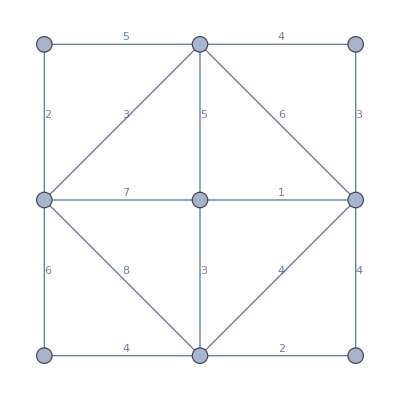

```mathematica
exercise3=Graph[{"a","b","c","d","e","f","g","h","i"},{"a"->"b","a"->"d","b"->"c","b"->"d","b"->"e","b"->"f","c"->"f","d"->"e","d"->"g","d"->"h","e"->"f","e"->"h","f"->"h","f"->"i","g"->"h","h"->"i"},DirectedEdges->False,EdgeWeight->{5,2,4,3,5,6,3,7,6,8,1,3,4,4,4,2},
VertexCoordinates->{{0,2},{1,2},{2,2},{0,1},{1,1},{2,1},{0,0},{1,0},{2,0}},VertexSize->Small,VertexLabels->Placed["Name",Center],EdgeLabels->Placed["EdgeWeight",{.5,{-1,0}}]]
```

The Wolfram Language GraphDistance function accepts two or three arguments. Given a graph and two vertices in the graph, it returns the distance between the two vertices. For example, in the graph above, we compute the distance from c to e as follows.

```mathematica
GraphDistance[exercise3,"c","e"]
```

4.

You can also apply GraphDistance to a graph and just one of its vertices. In this case, the output will be a list of the shortest distances from the given vertex to each of the vertices in the graph. For example, the following shows the distances from the central vertex e to each of the vertices in the graph. The 0 in the output corresponds to the distance from the vertex to itself.

```mathematica
GraphDistance[exercise3,"e"]
```

{9.,5.,4.,7.,0,1.,7.,3.,5.}

The GraphDistanceMatrix function applied to a graph produces the matrix whose entries are the distances between corresponding vertices. The rows and columns are ordered according to the order of vertices in the graph, agreeing with the output of VertexList.

```mathematica
GraphDistanceMatrix[exercise3]//MatrixForm
```

(0. | 5. | 9. | 2. | 9. | 10. | 8. | 10. | 12.
5. | 0. | 4. | 3. | 5. | 6. | 9. | 8. | 10.
9. | 4. | 0. | 7. | 4. | 3. | 11. | 7. | 7.
2. | 3. | 7. | 0. | 7. | 8. | 6. | 8. | 10.
9. | 5. | 4. | 7. | 0. | 1. | 7. | 3. | 5.
10. | 6. | 3. | 8. | 1. | 0. | 8. | 4. | 4.
8. | 9. | 11. | 6. | 7. | 8. | 0. | 4. | 6.
10. | 8. | 7. | 8. | 3. | 4. | 4. | 0. | 2.
12. | 10. | 7. | 10. | 5. | 4. | 6. | 2. | 0.)

Using TableForm and the TableHeadings option, we can easily create a table of the distances with row and column headings making the vertices explicit. TableHeadings is associated with a list of two lists in order to label the rows and columns.

```mathematica
TableForm[GraphDistanceMatrix[exercise3],TableHeadings->{VertexList[exercise3],VertexList[exercise3]}]
```

| a | b | c | d | e | f | g | h | i
a | 0. | 5. | 9. | 2. | 9. | 10. | 8. | 10. | 12.
b | 5. | 0. | 4. | 3. | 5. | 6. | 9. | 8. | 10.
c | 9. | 4. | 0. | 7. | 4. | 3. | 11. | 7. | 7.
d | 2. | 3. | 7. | 0. | 7. | 8. | 6. | 8. | 10.
e | 9. | 5. | 4. | 7. | 0. | 1. | 7. | 3. | 5.
f | 10. | 6. | 3. | 8. | 1. | 0. | 8. | 4. | 4.
g | 8. | 9. | 11. | 6. | 7. | 8. | 0. | 4. | 6.
h | 10. | 8. | 7. | 8. | 3. | 4. | 4. | 0. | 2.
i | 12. | 10. | 7. | 10. | 5. | 4. | 6. | 2. | 0.

### Prim’s Algorithm

We will now build functions to implement Prim’s algorithm. We will also see how to create animations that illustrate the process of building the spanning tree.

Since both Prim’s algorithm and Kruskal’s depend on choosing an edge of smallest weight, it will be useful to be able to apply Sort to a list of edges. Recall that Sort accepts an optional second argument: a function that takes two arguments and returns True if the first argument is less than the second. Our function will need to access the edge weight with PropertyValue, which also requires the graph as an argument. Therefore, we will create a function that takes a graph as the argument and produces a pure Function (&) that requires only the two edges as arguments.

```mathematica
edgeCompare[G_]:=Function[{e1,e2},
PropertyValue[{G,e1},EdgeWeight]<PropertyValue[{G,e2},EdgeWeight]
]
```

The list we provided to Function as its first argument specifies that the symbols e1 and e2 will be interpreted as parameters, in place of the generic Slot (#).

Applying edgeCompare to a graph will output a function. Assigning the result to a symbol means that symbol can then be used as a function. The expression below will cause testComp to act as a function on two argument, edges in exercise3, and return True if the weight of the first is less than or equal to the weight of the second.

```mathematica
testComp=edgeCompare[exercise3]
```

Function[{e1$,e2$},PropertyValue[{-Graphics-,e1$},EdgeWeight]<PropertyValue[{-Graphics-,e2$},EdgeWeight]]

```mathematica
testComp["a"<->"d","a"<->"b"]
```

True

Prim’s algorithm is given as Algorithm 1 in Section 11.5 of the textbook. It constructs a minimum spanning tree by successively selecting an edge of smallest weight that extends the tree without creating any loops.

To simplify our implementation of Prim’s algorithm, we will create a function minEdge. Given the original graph and the list of vertices already included in the spanning tree, minEdge determines which edge of the graph should be added next.

minEdge first needs to determine the set of edges that are incident with a vertex currently in the tree. It will do this by applying NeighborhoodGraph to the graph and the list of vertices in the tree. The minEdge function then eliminates any edge with both ends already in the spanning tree or neither end in the spanning tree. (This is equivalent to the condition that the edge not introduce a simple circuit but that the new graph will be connected.) Once it has determined the valid candidates, the minEdge function returns the edge with smallest weight. We also include the special case that the spanning tree has not yet been started, in which case we call the function with the empty list as the second argument.

```mathematica
minEdge[G_Graph,V_List]:=Module[{possibleEdges,i},
If[V=={},
(* empty tree case *)
possibleEdges=EdgeList[G],
(* nonempty case *)
possibleEdges=EdgeList[NeighborhoodGraph[G,V]];
i=1;
While[i≤Length[possibleEdges],
If[MemberQ[V,possibleEdges[[i]][[1]]]==MemberQ[V,possibleEdges[[i]][[2]]],
possibleEdges=Delete[possibleEdges,i],
i++]
]
];
If[possibleEdges=={},Return[Null]];
possibleEdges=Sort[possibleEdges,edgeCompare[G]];
possibleEdges[[1]]
]
```

With this function in place, Prim’s algorithm is fairly straightforward to implement.

Begin building the spanning tree by finding the edge of minimum weight by calling the function minEdge on the graph and the empty list.

Continue building the spanning tree one edge at a time by adding the edge returned by minEdge. (Note that we must add the new vertex before the edge, since EdgeAdd expects both endpoints of the edge to be added to already be in the graph.)

After n-2 repetitions of step 2, where n is the number of vertices in the graph, the spanning tree is complete.

```mathematica
prim[G_Graph,opts___]:=Module[{newEdge,T,n,i,v},
newEdge=minEdge[G,{}];
T=Graph[{newEdge},opts];
PropertyValue[{T,newEdge},EdgeWeight]=PropertyValue[{G,newEdge},EdgeWeight];
PropertyValue[{T,newEdge},EdgeLabels]=PropertyValue[{G,newEdge},EdgeWeight];
n=VertexCount[G];
For[i=1,i≤n-2,i++,
newEdge=minEdge[G,VertexList[T]];
If[VertexQ[T,newEdge[[1]]],
T=VertexAdd[T,newEdge[[2]]],
T=VertexAdd[T,newEdge[[1]]]
];
T=EdgeAdd[T,newEdge];
PropertyValue[{T,newEdge},EdgeWeight]=PropertyValue[{G,newEdge},EdgeWeight];
PropertyValue[{T,newEdge},EdgeLabels]=PropertyValue[{G,newEdge},EdgeWeight]
];
T
]
```

We can now use this algorithm to find the minimum spanning tree for Exercise 3.

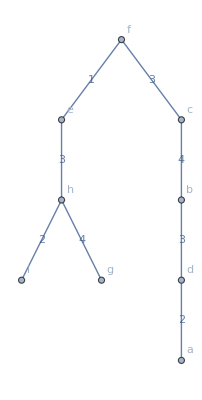

```mathematica
primExercise3=prim[exercise3,VertexLabels->"Name"]
```

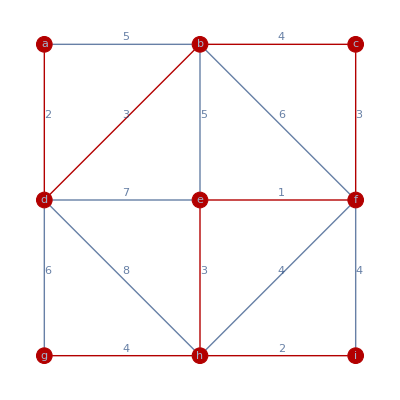

```mathematica
HighlightGraph[exercise3,primExercise3]
```

Before moving on to Kruskal’s algorithm, we create a function to produce an animation demonstrating Prim’s algorithm in action. First, we modify the prim function to record the list of edges that form the tree and return this list of edges rather than the tree.

```mathematica
primEdges[G_Graph]:=Module[{newEdge,T,edgeList,n,i,v},
newEdge=minEdge[G,{}];
T=Graph[{newEdge}];
edgeList={newEdge};
n=VertexCount[G];
For[i=1,i≤n-2,i++,
newEdge=minEdge[G,VertexList[T]];
If[VertexQ[T,newEdge[[1]]],
T=VertexAdd[T,newEdge[[2]]],
T=VertexAdd[T,newEdge[[1]]]
];
T=EdgeAdd[T,newEdge];
AppendTo[edgeList,newEdge]
];
edgeList
]
```

```mathematica
primEdges[exercise3]
```

{e<->f,c<->f,e<->h,h<->i,g<->h,b<->c,b<->d,a<->d}

We now write the function that will produce the animation. Since this is nearly identical to the animatePath function from Chapter 10, we refer the reader to Section 10.5 of this manual for a detailed explanation.

```mathematica
animateTree[G_Graph,T_List,opts___]:=Module[{i,len},
len=Length[T];
Animate[HighlightGraph[G,T[[1;;i]],opts],{{i,0,"step"},0,len,1},AnimationRunning->False,AnimationRepetitions->1]
]
```

```mathematica
animateTree[exercise3,primEdges[exercise3]]
```

### Kruskal’s Algorithm

Recall that Kruskal’s algorithm, Algorithm 2 in Section 11.5, begins in the same way as Prim’s algorithm, with the edge of smallest weight. The difference is that at each step, Kruskal’s algorithm adds whatever edge is of least weight which does not create a simple circuit, regardless of whether it is incident to an edge already in the graph.

We begin with a function to test whether or not a given edge will create a simple circuit. Note that, during the steps of Kruskal’s algorithm, we have a forest of trees. An edge will create a simple circuit if and only if both of its endpoints are in the same tree within the forest. We use the ConnectedComponents function to find the trees. The ConnectedComponents function returns a list of lists, where each inner list is the vertices within one of the connected components of the graph. We test an edge by looping through each of the connected components and making sure that both ends do not appear in the same component.

```mathematica
noCircuitQ[G_Graph,edge_]:=Module[{components,C},
components=ConnectedComponents[G];
Catch[
Do[If[MemberQ[C,edge[[1]]]&&MemberQ[C,edge[[2]]],Throw[False]]
,{C,components}];
Throw[True]
]
]
```

We now implement Kruskal’s algorithm. The function is as follows.

Initialize edges to the list of edges of the given graph and sort this list using the edgeCompare function created above.

Initialize T to the graph with all the vertices of G and no edges.

Consider the first edge in the edges list. Use noCircuitQ to determine if it is safe to add to the tree. If we can add it to the tree, add one or both of its ends as new vertices to T as needed and add the edge.

Regardless of whether noCircuitQ approves the addition of the first edge in edges to the tree, remove the edge from edges—either the edge is now used in the tree and so will not be used again, or its addition would create a circuit (a fact which will not change later).

Repeat steps 3 and 4 until n-1 edges have been added, where n is the number of vertices.

```mathematica
kruskal[G_Graph,opts___]:=Module[{edges,T,n,i,newEdge,v},
edges=Sort[EdgeList[G],edgeCompare[G]];
T=Graph[VertexList[G],{},opts];
n=VertexCount[G];
i=1;
While[i≤n-1,
newEdge=edges[[1]];
If[noCircuitQ[T,newEdge],
T=EdgeAdd[T,newEdge];
PropertyValue[{T,newEdge},EdgeWeight]=PropertyValue[{G,newEdge},EdgeWeight];
PropertyValue[{T,newEdge},EdgeLabels]=PropertyValue[{G,newEdge},EdgeWeight];
i++
];
edges=Delete[edges,1]
];
T
]
```

Note that Kruskal’s algorithm produces the same minimum spanning tree for Exercise 3 as did our implementation of Prim’s algorithm (in fact, this graph has a unique minimum spanning tree).

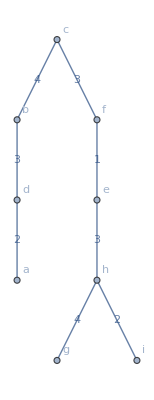

```mathematica
kruskal[exercise3,VertexLabels->"Name"]
```

We can produce an animation, like we did for Prim’s algorithm, by modifying the function to produce the list of edges in the order they are added and then using the animateTree function once again.

```mathematica
kruskalEdges[G_Graph]:=Module[{edges,edgeList,T,n,i,newEdge,v},
edges=Sort[EdgeList[G],edgeCompare[G]];
edgeList={};
T=Graph[VertexList[G],{}];
n=VertexCount[G];
i=1;
While[i≤n-1,
newEdge=edges[[1]];
If[noCircuitQ[T,newEdge],
T=EdgeAdd[T,newEdge];
AppendTo[edgeList,newEdge];
i++
];
edges=Delete[edges,1]
];
edgeList
]
```

```mathematica
animateTree[exercise3,kruskalEdges[exercise3]]
```

By comparing the two animations, you can see how the two algorithms provide different routes to the same end result.

## Solutions to Computer Projects and Computations and Explorations

### Computer Projects 6

Given the ordered list of edges of an ordered rooted tree, find the universal addresses of its vertices.

Solution: Recall that the universal address of a vertex in an ordered rooted tree is defined as follows. The root has address 0 and its children have addresses 1, 2, 3, etc., in order. The address of every other vertex is defined recursively as p.n where p is the address of the vertex’s parent and n is 1 if the vertex is the first child of its parent, 2 if it is the second child, etc.

Before solving this problem, we will make the following assumption on the input, as per the problem statement: the edges are sorted according to the lexicographical order of the universal address of their terminal vertex. That is to say, the edges are listed in the order of their appearance from left to right and top to bottom when the tree is drawn in the usual way.

We build the ordered rooted tree (satisfying orderedRootedTreeQ) determined by the list of edges and add a “univ-address” property to each vertex containing the vertex’s universal address. First, here is an ordered list of edges for an ordered rooted tree.

```mathematica
cp6Example={"D"->"E","D"->"C","D"->"I","E"->"L","E"->"F","I"->"B","I"->"K","I"->"H","F"->"J","F"->"G","F"->"A"}
```

{D→E,D→C,D→I,E→L,E→F,I→B,I→K,I→H,F→J,F→G,F→A}

We have purposefully chosen vertex names that are out of order with respect to the ordering of the edges so that our construction is sure to rely only on the ordering of the edges and not on the vertex labels.

Note that creating a graph with these edges only requires passing it to the Graph function.

```mathematica
cp6Graph=Graph[cp6Example];
```

Our first task is to turn this into an ordered rooted tree. Since we provided directed edges, it is already a rooted tree.

```mathematica
rootedTreeQ[cp6Graph]
```

True

To make this graph an ordered rooted tree, we need to set the “order” property for each vertex. For the root, we just set the root’s “order” to 0.

```mathematica
PropertyValue[{cp6Graph,findRoot[cp6Graph]},"order"]=0
```

0

For the rest of the vertices, we need to do some more work. Our approach will be as follows. Loop through all of the edges in the original edge list, in order, keeping track of two variables, curParent, the current parent, and the childOrder. The curParent will initially be set to the root of the tree and childOrder will be initialized to 1. For the first edge in the list, we assign the child vertex (the terminal vertex of the ordered edge) “order” equal to childOrder. We then go to the next edge. If the curParent is the same as the parent vertex in this edge, then childOrder is incremented and we assign the child vertex of this edge an order equal to the new childOrder value. Otherwise, the parent vertex of this new edge is different from curParent. This indicates that we have moved on to a new parent with a new set of children, so we set curParent to this new parent and reset childOrder to 1. Here is the code for this step in the process.

```mathematica
curParent=findRoot[cp6Graph];
childOrder=1;
Do[If[thisEdge[[1]]≠curParent,
curParent=thisEdge[[1]];
childOrder=1];
PropertyValue[{cp6Graph,thisEdge[[2]]},"order"]=childOrder;
childOrder++
,{thisEdge,cp6Example}]
```

Now that the order attributes are set, our graph is an ordered rooted tree.

```mathematica
orderedRootedTreeQ[cp6Graph]
```

True

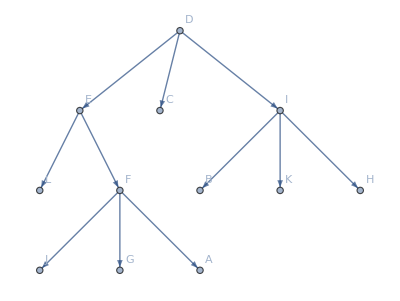

```mathematica
Graph[cp6Graph,VertexLabels->"Name"]
```

We use the approach above to define a function.

```mathematica
treeFromList[L_List,opts___]:=Module[{T,e,curParent,childOrder,thisEdge},
T=Graph[L,opts];
PropertyValue[{T,findRoot[T]},"order"]=0;
curParent=findRoot[T];
childOrder=1;
Do[If[thisEdge[[1]]≠curParent,
curParent=thisEdge[[1]];
childOrder=1
];
PropertyValue[{T,thisEdge[[2]]},"order"]=childOrder;
childOrder++
,{thisEdge,L}];
T
]
```

We could now create a function that uses the pattern of a breadth first search to assign the universal addresses. Instead, we will take this opportunity to use the built-in function BreadthFirstScan instead. The first two arguments will be the graph and the root of the graph, which explicitly indicates where to begin the breadth first search. The third argument will be a list specifying a function to use when the event “DiscoverVertex” occurs. The function is applied to two arguments, #1 refers to the vertex being discovered, and #2 refers to the vertex from which it is discovered, that is, its parent. The body of our function will check if the parent has “order” property 0, indicating that the discovered vertex is either the root or a child of the root. In this case, the “univ-address” property will be set to the vertex’s order. Otherwise, the “univ-address” will be set to the concatenation of the parent’s address and the vertex’s order.

```mathematica
universalAddress[edgeList_List,opts___]:=Module[{G},
G=treeFromList[edgeList,opts];
BreadthFirstScan[G,findRoot[G],{"DiscoverVertex"->
((If[PropertyValue[{G,#2},"order"]==0,
(* root or root's child *)
PropertyValue[{G,#1},"univ-address"]=ToString[PropertyValue[{G,#1},"order"]],
(* descendant of a root's child *)
PropertyValue[{G,#1},"univ-address"]=PropertyValue[{G,#2},"univ-address"]<>"."<>ToString[PropertyValue[{G,#1},"order"]]];
(* set address as vertex label *)
PropertyValue[{G,#1},VertexLabels]=PropertyValue[{G,#1},"univ-address"]
)&)}];
G
]
```

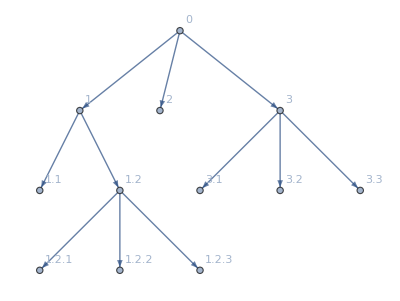

```mathematica
universalAddress[cp6Example]
```

### Computations and Explorations 1

Display all trees with six vertices.

Solution: To solve this problem, we make use of a recursive definition of tress. The empty graph is a tree, the graph with a single vertex is also a tree, and the graph with two vertices with an edge between them is a tree. Given any tree, we can form a new tree with one additional vertex by adding the new vertex as a leaf connected to any one of the original vertices. (The reader can verify that this indeed creates all trees with one more vertex.)

We shall create a function, called extendTrees, that accepts as input a list of trees on n vertices and returns the resulting list of trees on n+1 vertices. For each of the original trees, we consider each vertex of the tree and create a new tree by adding a leaf to it.

```mathematica
extendTrees[trees_List]:=Module[{newTrees,newV,T,v,newT},
newTrees={};
newV=VertexCount[trees[[1]]]+1;
Do[
Do[
newT=VertexAdd[T,newV];
newT=EdgeAdd[newT,v->newV];
AppendTo[newTrees,newT]
,{v,VertexList[T]}]
,{T,trees}];
newTrees
]
```

We can now use this procedure to determine all trees on four vertices. Finding all the trees of larger sizes is left to the reader.

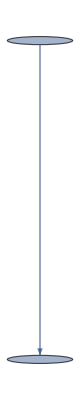

```mathematica
allTrees={Graph[{1,2},{1->2},DirectedEdges->True,GraphLayout->"LayeredDigraphEmbedding"]}
```

```mathematica
For[i=3,i≤4,i++,allTrees=extendTrees[allTrees]];
```

We now display the six trees on four vertices.

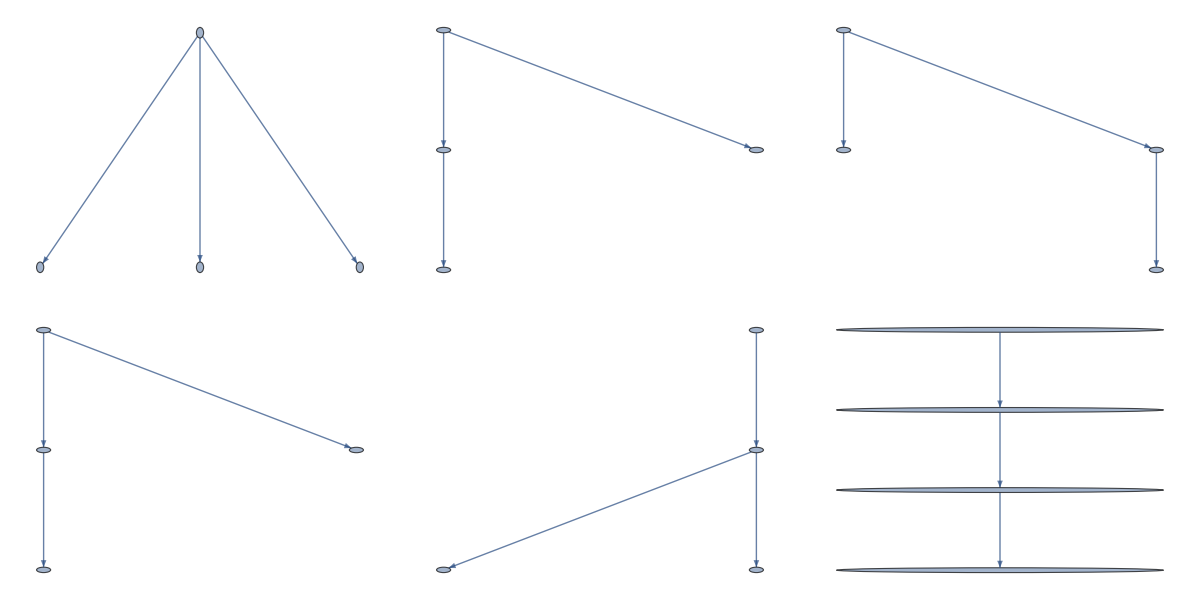

```mathematica
Grid[Partition[allTrees,3],Frame->All]
```

### Computations and Explorations 3

Construct a Huffman code for the symbols with ASCII codes given the frequency of their occurrence in representative input.

Solution: ASCII, which stands for American Standard Code for Information Interchange, includes 128 characters, including 33 non-printing characters. Most of the non-printing characters, with the exception of the space and the carriage return or newline character, however, are rarely used. We will focus on the standard characters of English and the newline character.

Since we have already created the function, huffmanCode, which creates a Huffman code based on a list of character/weight pairs, the main work we need to do is determine the frequencies of characters in a sample input. We use the following input, which contains letters, punctuation, and newline characters.

```mathematica
inputText="The quick brown fox said,
\"How do you do, my friend?\"
Then he ran very quickly off into the sunset."
```

The quick brown fox said,
"How do you do, my friend?"
Then he ran very quickly off into the sunset.

We can turn this string into a list by applying the Characters function.

```mathematica
textList=Characters[inputText]
```

{T,h,e, ,q,u,i,c,k, ,b,r,o,w,n, ,f,o,x, ,s,a,i,d,,,
,",H,o,w, ,d,o, ,y,o,u, ,d,o,,, ,m,y, ,f,r,i,e,n,d,?,",
,T,h,e,n, ,h,e, ,r,a,n, ,v,e,r,y, ,q,u,i,c,k,l,y, ,o,f,f, ,i,n,t,o, ,t,h,e, ,s,u,n,s,e,t,.}

Using FullForm, we can display the newline characters for us explicitly. Observe that the Wolfram Language differentiates between a newline character and a space character.

```mathematica
textList[[26]]//FullForm
```

"
"

```mathematica
textList[[4]]//FullForm
```

" "

```mathematica
textList[[26]]==textList[[4]]
```

False

We will calculate the frequencies of the characters in our text by applying the Tally function. When applied to a list, Tally returns a list of pairs consisting of the unique elements of the original list and the number of times each appears.

```mathematica
Tally[Characters[inputText]]
```

{{T,2},{h,4},{e,7},{ ,17},{q,2},{u,4},{i,5},{c,2},{k,2},{b,1},{r,4},{o,8},{w,2},{n,6},{f,4},{x,1},{s,3},{a,2},{d,4},{,,2},{
,2},{",2},{H,1},{y,4},{m,1},{?,1},{v,1},{l,1},{t,3},{.,1}}

The Huffman function expects the input to consist of the characters and their relative frequency. Thus, we need to divide the counts from the Tally output by the number of characters.

```mathematica
Length[Characters[inputText]]
```

99

```mathematica
foxList=Tally[Characters[inputText]]/.{c_,n_}->{c,n/99}
```

{{T,2/99},{h,4/99},{e,7/99},{ ,17/99},{q,2/99},{u,4/99},{i,5/99},{c,2/99},{k,2/99},{b,1/99},{r,4/99},{o,8/99},{w,2/99},{n,2/33},{f,4/99},{x,1/99},{s,1/33},{a,2/99},{d,4/99},{,,2/99},{
,2/99},{",2/99},{H,1/99},{y,4/99},{m,1/99},{?,1/99},{v,1/99},{l,1/99},{t,1/33},{.,1/99}}

Finally, we are able to apply the huffmanCode function.

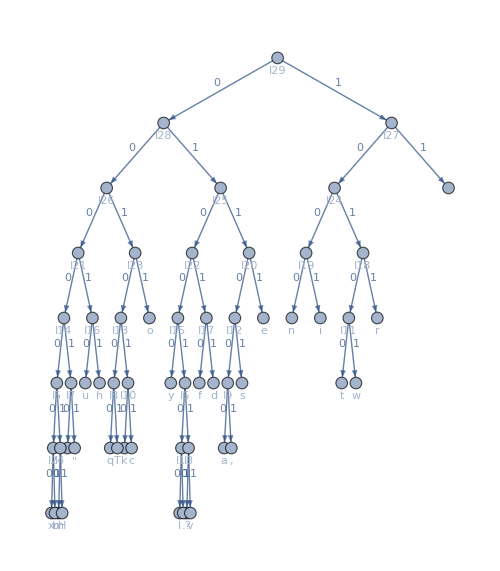

```mathematica
foxCode=huffmanCode[foxList,VertexLabels->Placed["Name",Below],ImageSize->500]
```

You will need to enlarge the image substantially in order to see the result in a readable format.

### Computations and Explorations 8

Draw the complete game tree for a game of checkers on a 4×4 board.

Solution: We will provide a partial solution to this problem; the reader is left to complete the full solution. Specifically, we will create a function called movePiece that will determine all possible new checker arrangements given the current state of the board and the player whose turn it is. Once this function is created, the reader must determine how to represent these board positions as vertices and edges, how to determine the next level of the game tree, as well as the halting conditions.

Before writing this function, however, we must establish a representation of the board. Naturally, we will use a matrix whose size is the size of the board. Empty board spaces will contain 0. Board spaces in which a regular white or black piece is sitting will be represented by 1 or 2, respectively. Kings will be represented by negative values, -1 for a white king and -2 for a black king. The following represents an initial board before any moves have been made.

```mathematica
checkersStart={{0,2,0,2},{0,0,0,0},{0,0,0,0},{1,0,1,0}};
checkersStart//MatrixForm
```

(0 | 2 | 0 | 2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 1 | 0)

Given a matrix representing a board state and an integer representing which side’s turn it is, the function movePiece will list all of the possible results of the player’s move. It operates as follows:

Initialize newBoards, which will be the list of all possible boards that result from the current move, to the empty list.

If side is 1, then normal pieces move up the board from bottom to top and we set direction to -1, since the index of rows in a matrix decrease as we move up the board. If the side is 2, then direction is set to +1.

Begin a pair of For loops, with indices r and c. These For loops allow us to consider each possible board location. In each position, we want to know if that location holds a piece belonging to the current player. If it is 1’s turn, then that player’s normal pieces are represented by a 1 in the position and the player’s kings are represented by a -1 in the position. Likewise, 2’s pieces are represent by 2 or by -2. Thus, we can determine if a position holds a player’s piece by comparing the absolute value of the matrix entry with the side. If the square does not hold a piece belonging to the current player, we simply move on to the next location.

Check to see if the piece is a king and set the variable isKing to 1 if it is a king or 0 if not. We then begin a For loop from 0 to the value of isKing. If isKing is 0, the loop executes only once. If isKing is 1, then the loop will execute twice. The index of this loop, king, is used to control rowDir, the current direction being considered. rowDir is either the same as direction or, in the case of the second iteration for a king, the reverse direction.

We now check to see if the possible moves keep the piece on the board. First, we make sure that r+rowDir, that is, the row in which the piece would move to, is still between 1 and 4 (the possible rows).

Assuming moving the piece would not take it off the top or bottom of the board, consider the left and right moves. We do this with a For loop which sets the variable colDir to -1 and then to +1. Again, we check to see that c+colDir, the current column plus the proposed change to the column position, is still on the board.

At this point we know that the board position (r+rowDir,c+colDir) is actually a board position. There are now three possibilities: the position is empty, there is an enemy piece in the square, there is a friendly piece in the square.

In the first case, the position is empty, we want to move the piece to that location. We make a copy of the board matrix (so we do not modify the original board). Then, we make the move and add the new board to the list. Note that we also check to see if the piece becomes a king by moving into this position.

In the second case, there is an enemy in the square, then we test to see if it is possible to jump. That is, we must make sure that the landing location after the jump is both on the board and empty. If so, we make the jump, that is, we copy the board and make the necessary modifications. If not, then the move is not possible.

In the third case, the move is not possible and we do nothing.

Here is the function.

```mathematica
movePiece[board_List,side_Integer]:=Module[{newBoards={},direction,r,c,isKing,king,rowDir,colDir,newB},
direction=Switch[side,1,-1,2,1];
For[r=1,r≤4,r++,
For[c=1,c≤4,c++,
If[Abs[board[[r,c]]]==side,
If[board[[r,c]]<0,isKing=1,isKing=0];
For[king=0,king≤isKing,king++,
rowDir=Switch[king,0,direction,1,-direction];
If[r+rowDir≥1&&r+rowDir≤4,
For[colDir=-1,colDir≤1,colDir=colDir+2,
If[c+colDir≥1&&c+colDir≤4,
Which[board[[r+rowDir,c+colDir]]==0,
newB=board;
If[((r+rowDir==1&&side==1)||(r+rowDir==4&&side==2))&&board[[r,c]]>0,
newB[[r+rowDir,c+colDir]]=-1*board[[r,c]],
newB[[r+rowDir,c+colDir]]=board[[r,c]]
];
newB[[r,c]]=0;
AppendTo[newBoards,newB],
Abs[board[[r+rowDir,c+colDir]]]≠side,
If[r+2*rowDir≥1&&r+2*rowDir≤4&&c+2*colDir≥1&&c+2*colDir≤4,
If[board[[r+2*rowDir,c+2*colDir]]==0,
newB=board;
If[((r+2*rowDir==1&&side==1)||(r+2*rowDir==4&&side==2))&&board[[r,c]]>0,newB[[r+2*rowDir,c+2*colDir]]=-board[[r,c]],
newB[[r+2*rowDir,c+2*colDir]]=board[[r,c]]
];
newB[[r,c]]=0;
newB[[r+rowDir,c+colDir]]=0;
AppendTo[newBoards,newB]
]
]
]
]
]
]
]
]
]
];
newBoards
]
```

We now demonstrate a few steps using the function.

```mathematica
move1=movePiece[checkersStart,1];
MatrixForm/@move1
```

{(0 | 2 | 0 | 2
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0),(0 | 2 | 0 | 2
0 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 2 | 0 | 2
0 | 0 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0)}

```mathematica
move2=movePiece[move1[[1]],2];
MatrixForm/@move2
```

{(0 | 0 | 0 | 2
2 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 2
0 | 0 | 2 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0),(0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)}

```mathematica
move3=movePiece[move2[[3]],1];
MatrixForm/@move3
```

{(0 | 2 | 0 | 0
1 | 0 | 2 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 2 | 0 | -1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 1 | 0 | 1
0 | 0 | 0 | 0)}

```mathematica
move4=movePiece[move3[[2]],2];
MatrixForm/@move4
```

{(0 | 0 | 0 | -1
2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | -1
0 | 0 | 2 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)}

## Exercises

Write Wolfram Language functions for finding the eccentricity of a vertex in an unrooted tree and for finding the center of an unrooted tree. (Eccentricity and center are defined in prelude to Exercise 39 of Section 11.1 of the text.)

Develop a function in the Wolfram Language for constructing rooted Fibonacci trees. (See the prelude to Exercise 45 of Section 11.1 for a definition of a Fibonacci tree.)

Develop a function in the Wolfram Language for listing the vertices of an ordered rooted tree in level order.

Compare the performance of binary search trees to linear search as follows:

Write a function, linearSearch, that takes two inputs, a list of integers and an integer to find, and checks each element of the list in order until the input is found, at which time it returns True. If the desired integer is not found, it is added the end of the list.

Use the function RandomSample[Range[n],n] for a positive integer n to create a list of the first n integers in random order, with an appropriately large n. Apply the makeBST function to the list to create a binary search tree for the data.

Randomly select some positive integers to search for. The RandomInteger function could be useful here.

Use both linearSearch and binaryInsertion to find the integers from part c in the list and tree, respectively. Time them using the typical Timing function. Repeat this for 100 different initial lists of integers and compare the resulting times. Compare these data (representing average-case complexity) with the theoretical worst-case results of n comparisons for linearSearch and log(n) for binaryInsertion.

Construct a function in the Wolfram Language for decoding a message which was encoded with a Huffman code. That is, given a Huffman coding tree produced by the HuffmanCode procedure and a message encoded by the encodeString function, the algorithm should return the original string.

Use the Shakespearean sonnets to estimate the frequency of characters used by Shakespeare. (See Section 7.3 of this manual to see how to read the data into Mathematica and make use of the functions given in the solution to Computations and Explorations 3 to compute the frequencies of characters used in the poems.) Then, create a Huffman code based on the sonnets and encode the ShakespeareData.txt with the Huffman code. Compare the storage space required by the Huffman encoded version of the file as opposed to the space that would be used to encode the file in ASCII format, assuming each ASCII character requires 7 bits.

Compare the performance of the breadth-first and depth-first functions for finding spanning trees. Use the RandomGraph function to create random trees. The expression RandomGraph[{v,e}] will create a random graph with v vertices and e edges, but you will need to ensure the graph is connected before applying the functions for creating the spanning tree.

Construct an undirected weighted graph which has at least two different minimum spanning trees and for which the prim and kruskal algorithms will return different results.

Write a function in the Wolfram Language implementing the reverse-delete algorithm for constructing minimal spanning trees. (The reverse-delete algorithm is described in the prelude to Exercise 34 in Section 11.5.)

Explore the relative complexity of prim, kruskal, and the reverse-delete function you created in the previous exercise. Use the RandomGraph function to experiment with their performance. The expression

RandomGraph[{v,e}, EdgeWeight → RandomInteger[{min,max},e]]

will produce a random weighted graph with v vertices and e edges with weights between min and max. You will then need to ensure that the random graph is connected. For each algorithm, can you find properties that you can impose on the graphs that will ensure that the algorithm will outperform the others?

Develop a Wolfram Language function for producing degree-constrained spanning trees, which are defined in the Supplementary Exercises for Chapter 11. Use this function on a set of randomly generated graphs to attempt to construct degree-constrained spanning trees in which each vertex has degree no larger than 3.

Use Mathematica to analyze the game of Nim with different starting conditions via the technique of game trees. (See Example 6 in Section 11.2 for a description of the game of Nim.)

Use Mathematica to analyze the game of checkers on square boards of different sizes via the technique of game trees. (See the solution to Computations and Explorations 8 for the beginnings of a solution.)

Develop functions in the Wolfram Language for finding a path through a maze using the technique of backtracking.

Develop functions for solving Sudoku puzzles using the technique of backtracking.

Use Mathematica to generate as many graceful trees as possible. (See the Supplementary Exercises of Chapter 11 for a definition of graceful.) Based on the examples you find, make conjectures about graceful trees.

Alter the postfix expression evaluator, evalPostfix, to handle prefix expressions.